# Tight binding model for MX2

## Particular values are taken from Xiao’s paper

## Eleven orbital model

### Parameters

```mathematica
Δ0=-1.016;
Δ1=0.;
Δ2=-2.529;
Δp=-0.780;
Δz=-7.740;
Vpds=-2.619;
Vpdp=-1.396;
Vdds=-0.933;
Vddp=-0.478;
Vddd=-0.442;
Vpps=0.696;
Vppp=0.278;
```

### Hopping integrals

#### tpda

```mathematica
taxz2=1./(7. √7.)(√3. Vpds -9. Vpdp);
taxx2=1./(7. √7.)(3. Vpds+5. √3. Vpdp);
taxxy=-1./(7. √7.)(3. √3. Vpds+Vpdp);
taxxzt=1./(7. √7.)(9. Vpds+√3. Vpdp);
taxxzb=-1./(7. √7.)(9. Vpds+√3. Vpdp);
taxyzt=1./(7. √7.)(-3. √3. Vpds+6. Vpdp);
taxyzb=-1./(7. √7.)(-3. √3. Vpds+6. Vpdp);
```

```mathematica
tayz2=1./(7. √7.)(-Vpds+3. √3. Vpdp);
tayx2=1./(7. √7.)(-√3. Vpds+9. Vpdp);
tayxy=1./(7. √7.)(3. Vpds+5. √3. Vpdp);
tayxzt=1./(7. √7.)(-3. √3. Vpds+6. Vpdp);
tayxzb=-1./(7. √7.)(-3. √3. Vpds+6. Vpdp);
tayyzt=1./(7. √7.) (3. Vpds+5. √3. Vpdp);
tayyzb=-1./(7. √7.) (3. Vpds+5. √3. Vpdp);
```

```mathematica
tazz2t=1./(7. √7.) (√3. Vpds+12. Vpdp);
tazz2b=-1./(7. √7.) (√3. Vpds+12. Vpdp);
tazx2t=1./(7. √7.) (3. Vpds-2. √3. Vpdp);
tazx2b=-1./(7. √7.) (3. Vpds-2. √3. Vpdp);
tazxyt=1./(7. √7.) (-3. √3. Vpds+6. Vpdp);
tazxyb=-1./(7. √7.) (-3. √3. Vpds+6. Vpdp);
tazxz=1./(7. √7.) (9. Vpds+√3. Vpdp);
tazyz=-1./(7. √7.) (3. √3. Vpds+Vpdp);
```

#### tpdb

```mathematica
tbxz2=0.;
tbxx2=0.;
tbxxy=2./(√7.) Vpdp;
tbxxzt=(√3.)/(√7.) Vpdp;
tbxxzb=-(√3.)/(√7.) Vpdp;
tbxyz=0.;
```

```mathematica
tbyz2=1./(7. √7.) (2. Vpds-6. √3. Vpdp);
tbyx2=-(√3.)/(7. √7.) (4. Vpds+2. √3. Vpdp);
tbyxy=0.;
tbyxz=0.;
tbyyzt=1./(7. √7.) (12. Vpds-√3. Vpdp);
tbyyzb=-1./(7. √7.) (12. Vpds-√3. Vpdp);
```

```mathematica
tbzz2t=1./(7. √7.) (√3. Vpds+12. Vpdp);
tbzz2b=-1./(7. √7.) (√3. Vpds+12. Vpdp);
tbzx2t=1./(7. √7.) (-6. Vpds+4. √3. Vpdp);
tbzx2b=-1./(7. √7.) (-6. Vpds+4. √3. Vpdp);
tbzxy=0.;
tbzxz=0.;
tbzyz=1./(7. √7.) (6. √3. Vpds+2. Vpdp);
```

#### tpdg

```mathematica
tgxz2=-1./(7. √7.)(√3. Vpds -9. Vpdp);
tgxx2=-1./(7. √7.)(3. Vpds+5. √3. Vpdp);
tgxxy=-1./(7. √7.)(3. √3. Vpds+Vpdp);
tgxxzt=1./(7. √7.)(9. Vpds+√3. Vpdp);
tgxxzb=-1./(7. √7.)(9. Vpds+√3. Vpdp);
tgxyzt=-1./(7. √7.)(-3. √3. Vpds+6. Vpdp);
tgxyzb=1./(7. √7.)(-3. √3. Vpds+6. Vpdp);
```

```mathematica
tgyz2=1./(7. √7.)(-Vpds+3. √3. Vpdp);
tgyx2=1./(7. √7.)(-√3. Vpds+9. Vpdp);
tgyxy=-1./(7. √7.)(3. Vpds+5. √3. Vpdp);
tgyxzt=-1./(7. √7.)(-3. √3. Vpds+6. Vpdp);
tgyxzb=1./(7. √7.)(-3. √3. Vpds+6. Vpdp);
tgyyzt=1./(7. √7.) (3. Vpds+5. √3. Vpdp);
tgyyzb=-1./(7. √7.) (3. Vpds+5. √3. Vpdp);
```

```mathematica
tgzz2t=1./(7. √7.) (√3. Vpds+12. Vpdp);
tgzz2b=-1./(7. √7.) (√3. Vpds+12. Vpdp);
tgzx2t=1./(7. √7.) (3. Vpds-2. √3. Vpdp);
tgzx2b=-1./(7. √7.) (3. Vpds-2. √3. Vpdp);
tgzxyt=-1./(7. √7.) (-3. √3. Vpds+6. Vpdp);
tgzxyb=1./(7. √7.) (-3. √3. Vpds+6. Vpdp);
tgzxz=-1./(7. √7.) (9. Vpds+√3. Vpdp);
tgzyz=-1./(7. √7.) (3. √3. Vpds+Vpdp);
```

#### tpp

```mathematica
taxx=1./4. (Vpps+3. Vppp);
taxy=(√3.)/4. (-Vpps+Vppp);
taxz=0.;
tayy=1./4. (3. Vpps+Vppp);
tayz=0.;
tazz=Vppp;
```

```mathematica
tbxx=Vpps;
tbyy=Vppp;
tbzz=Vppp;
```

```mathematica
tgxx=1./4. (Vpps+3. Vppp);
tgxy=(√3.)/4. (Vpps-Vppp);
tgxz=0.;
tgyy=1./4. (3. Vpps+Vppp);
tgyz=0.;
tgzz=Vppp;
```

#### tdda

```mathematica
taz2z2=1./4.(Vdds +3. Vddd);
taz2x2=(√3.)/8.(Vdds-Vddd);
taz2xy=3./8.(Vdds-Vddd);
taz2xz=0.;
taz2yz=0.;
```

```mathematica
tax2x2=1./16.(3. Vdds+12. Vddp+Vddd);
tax2xy=(√3.)/16.(3. Vdds-4. Vddp+Vddd);
tax2xz=0.;
tax2yz=0.;
```

```mathematica
taxyxy=1./16.(9. Vdds+4. Vddp+3.Vddd);
taxyxz=0.;
taxyyz=0.;
```

```mathematica
taxzxz=1./4. (Vddp+3. Vddd);
taxzyz=(√3.)/4. (-Vddp+Vddd);
```

```mathematica
tayzyz=1./4. (3. Vddp+Vddd);
```

#### tddb

```mathematica
tbz2z2=1./4. (Vdds+3. Vddd);
tbz2x2=(√3.)/4. (-Vdds+Vddd);
tbz2xy=0.;
tbz2xz=0.;
tbz2yz=0.;
```

```mathematica
tbx2x2=1./4. (3. Vdds+Vddd);
tbx2xy=0.;
tbx2xz=0.;
tbx2yz=0.;
```

```mathematica
tbxyxy=Vddp;
tbxyxz=0.;
tbxyyz=0.;
```

```mathematica
tbxzxz=Vddp;
tbxzyz=0.;
```

```mathematica
tbyzyz=Vddd;
```

#### tddg

```mathematica
tgz2z2=1./4.(Vdds +3. Vddd);
tgz2x2=(√3.)/8.(Vdds-Vddd);
tgz2xy=3./8.(-Vdds+Vddd);
tgz2xz=0.;
tgz2yz=0.;
```

```mathematica
tgx2x2=1./16.(3. Vdds+12. Vddp+Vddd);
tgx2xy=(√3.)/16. (-3. Vdds+4. Vddp-Vddd);
tgx2xz=0.;
tgx2yz=0.;
```

```mathematica
tgxyxy=1./16.(9. Vdds+4. Vddp+3.Vddd);
tgxyxz=0.;
tgxyyz=0.;
```

```mathematica
tgxzxz=1./4. (Vddp+3. Vddd);
tgxzyz=(√3.)/4. (Vddp-Vddd);
```

```mathematica
tgyzyz=1./4. (3. Vddp+Vddd);
```

### Hamiltonian matrices

#### r, r

```mathematica
Hrr=Table[0.,{i,1,11},{j,1,11}];

Hrr[[1,1]]=Δp;
Hrr[[2,2]]=Δp;
Hrr[[3,3]]=Δz;
Hrr[[4,4]]=Δ0;
Hrr[[5,5]]=Δ2;
Hrr[[6,6]]=Δ2;
Hrr[[7,7]]=Δ1;
Hrr[[8,8]]=Δ1;
Hrr[[9,9]]=Δp;
Hrr[[10,10]]=Δp;
Hrr[[11,11]]=Δz;

Hrr[[1,4]]=taxz2;
Hrr[[1,5]]=taxx2;
Hrr[[1,6]]=taxxy;
Hrr[[1,7]]=taxxzt;
Hrr[[1,8]]=taxyzt;

Hrr[[2,4]]=tayz2;
Hrr[[2,5]]=tayx2;
Hrr[[2,6]]=tayxy;
Hrr[[2,7]]=tayxzt;
Hrr[[2,8]]=tayyzt;

Hrr[[3,4]]=tazz2t;
Hrr[[3,5]]=tazx2t;
Hrr[[3,6]]=tazxyt;
Hrr[[3,7]]=tazxz;
Hrr[[3,8]]=tazyz;

Hrr[[1,9]]=Vppp;
Hrr[[2,10]]=Vppp;
Hrr[[3,11]]=Vpps;

Hrr[[4,9]]=taxz2;
Hrr[[5,9]]=taxx2;
Hrr[[6,9]]=taxxy;
Hrr[[7,9]]=taxxzb;
Hrr[[8,9]]=taxyzb;

Hrr[[4,10]]=tayz2;
Hrr[[5,10]]=tayx2;
Hrr[[6,10]]=tayxy;
Hrr[[7,10]]=tayxzb;
Hrr[[8,10]]=tayyzb;

Hrr[[4,11]]=tazz2b;
Hrr[[5,11]]=tazx2b;
Hrr[[6,11]]=tazxyb;
Hrr[[7,11]]=tazxz;
Hrr[[8,11]]=tazyz;

For[i=2,i≤11,i++,
For[j=1,j<i,++j,
Hrr[[i,j]]=Hrr[[j,i]]
]
]
```

#### r, r+a1

```mathematica
Hrra1=Table[0.,{i,1,11},{j,1,11}];

Hrra1[[1,1]]=tbxx;
Hrra1[[2,2]]=tbyy;
Hrra1[[3,3]]=tbzz;

Hrra1[[4,1]]=tgxz2;
Hrra1[[5,1]]=tgxx2;
Hrra1[[6,1]]=tgxxy;
Hrra1[[7,1]]=tgxxzt;
Hrra1[[8,1]]=tgxyzt;

Hrra1[[4,2]]=tgyz2;
Hrra1[[5,2]]=tgyx2;
Hrra1[[6,2]]=tgyxy;
Hrra1[[7,2]]=tgyxzt;
Hrra1[[8,2]]=tgyyzt;

Hrra1[[4,3]]=tgzz2t;
Hrra1[[5,3]]=tgzx2t;
Hrra1[[6,3]]=tgzxyt;
Hrra1[[7,3]]=tgzxz;
Hrra1[[8,3]]=tgzyz;

Hrra1[[4,9]]=tgxz2;
Hrra1[[5,9]]=tgxx2;
Hrra1[[6,9]]=tgxxy;
Hrra1[[7,9]]=tgxxzb;
Hrra1[[8,9]]=tgxyzb;

Hrra1[[4,10]]=tgyz2;
Hrra1[[5,10]]=tgyx2;
Hrra1[[6,10]]=tgyxy;
Hrra1[[7,10]]=tgyxzb;
Hrra1[[8,10]]=tgyyzb;

Hrra1[[4,11]]=tgzz2b;
Hrra1[[5,11]]=tgzx2b;
Hrra1[[6,11]]=tgzxyb;
Hrra1[[7,11]]=tgzxz;
Hrra1[[8,11]]=tgzyz;

Hrra1[[4,4]]=tbz2z2;
Hrra1[[4,5]]=tbz2x2;
Hrra1[[4,6]]=tbz2xy;
Hrra1[[4,7]]=tbz2xz;
Hrra1[[4,8]]=tbz2yz;

Hrra1[[5,4]]=tbz2x2;
Hrra1[[5,5]]=tbx2x2;
Hrra1[[5,6]]=tbx2xy;
Hrra1[[5,7]]=tbx2xz;
Hrra1[[5,8]]=tbx2yz;

Hrra1[[6,4]]=tbz2xy;
Hrra1[[6,5]]=tbx2xy;
Hrra1[[6,6]]=tbxyxy;
Hrra1[[6,7]]=tbxyxz;
Hrra1[[6,8]]=tbxyyz;

Hrra1[[7,4]]=tbz2xz;
Hrra1[[7,5]]=tbx2xz;
Hrra1[[7,6]]=tbxyxz;
Hrra1[[7,7]]=tbxzxz;
Hrra1[[7,8]]=tbxzyz;

Hrra1[[8,4]]=tbz2yz;
Hrra1[[8,5]]=tbx2yz;
Hrra1[[8,6]]=tbxyyz;
Hrra1[[8,7]]=tbxzyz;
Hrra1[[8,8]]=tbyzyz;

Hrra1[[9,9]]=tbxx;
Hrra1[[10,10]]=tbyy;
Hrra1[[11,11]]=tbzz;
```

#### r, r+a1-a2 && r, r-a1+a2

```mathematica
Hrra1a2=Table[0.,{i,1,11},{j,1,11}];

Hrra1a2[[1,1]]=tgxx;
Hrra1a2[[1,2]]=tgxy;
Hrra1a2[[1,3]]=tgxz;

Hrra1a2[[2,1]]=tgxy;
Hrra1a2[[2,2]]=tgyy;
Hrra1a2[[2,3]]=tgyz;

Hrra1a2[[3,1]]=tgxz;
Hrra1a2[[3,2]]=tgyz;
Hrra1a2[[3,3]]=tgzz;

Hrra1a2[[4,4]]=tgz2z2;
Hrra1a2[[4,5]]=tgz2x2;
Hrra1a2[[4,6]]=tgz2xy;
Hrra1a2[[4,7]]=tgz2xz;
Hrra1a2[[4,8]]=tgz2yz;

Hrra1a2[[5,4]]=tgz2x2;
Hrra1a2[[5,5]]=tgx2x2;
Hrra1a2[[5,6]]=tgx2xy;
Hrra1a2[[5,7]]=tgx2xz;
Hrra1a2[[5,8]]=tgx2yz;

Hrra1a2[[6,4]]=tgz2xy;
Hrra1a2[[6,5]]=tgx2xy;
Hrra1a2[[6,6]]=tgxyxy;
Hrra1a2[[6,7]]=tgxyxz;
Hrra1a2[[6,8]]=tgxyyz;

Hrra1a2[[7,4]]=tgz2xz;
Hrra1a2[[7,5]]=tgx2xz;
Hrra1a2[[7,6]]=tgxyxz;
Hrra1a2[[7,7]]=tgxzxz;
Hrra1a2[[7,8]]=tgxzyz;

Hrra1a2[[8,4]]=tgz2yz;
Hrra1a2[[8,5]]=tgx2yz;
Hrra1a2[[8,6]]=tgxyyz;
Hrra1a2[[8,7]]=tgxzyz;
Hrra1a2[[8,8]]=tgyzyz;

Hrra1a2[[9,9]]=tgxx;
Hrra1a2[[9,10]]=tgxy;
Hrra1a2[[9,11]]=tgxz;

Hrra1a2[[10,9]]=tgxy;
Hrra1a2[[10,10]]=tgyy;
Hrra1a2[[10,11]]=tgyz;

Hrra1a2[[11,9]]=tgxz;
Hrra1a2[[11,10]]=tgyz;
Hrra1a2[[11,11]]=tgzz;
```

#### r, r-a2

```mathematica
Hrra2m=Table[0.,{i,1,11},{j,1,11}];

Hrra2m[[1,1]]=taxx;
Hrra2m[[1,2]]=taxy;
Hrra2m[[1,3]]=taxz;

Hrra2m[[2,1]]=taxy;
Hrra2m[[2,2]]=tayy;
Hrra2m[[2,3]]=tayz;

Hrra2m[[3,1]]=taxz;
Hrra2m[[3,2]]=tayz;
Hrra2m[[3,3]]=tazz;

Hrra2m[[1,4]]=tbxz2;
Hrra2m[[1,5]]=tbxx2;
Hrra2m[[1,6]]=tbxxy;
Hrra2m[[1,7]]=tbxxzt;
Hrra2m[[1,8]]=tbxyz;

Hrra2m[[2,4]]=tbyz2;
Hrra2m[[2,5]]=tbyx2;
Hrra2m[[2,6]]=tbyxy;
Hrra2m[[2,7]]=tbyxz;
Hrra2m[[2,8]]=tbyyzt;

Hrra2m[[3,4]]=tbzz2t;
Hrra2m[[3,5]]=tbzx2t;
Hrra2m[[3,6]]=tbzxy;
Hrra2m[[3,7]]=tbzxz;
Hrra2m[[3,8]]=tbzyz;

Hrra2m[[4,4]]=taz2z2;
Hrra2m[[4,5]]=taz2x2;
Hrra2m[[4,6]]=taz2xy;
Hrra2m[[4,7]]=taz2xz;
Hrra2m[[4,8]]=taz2yz;

Hrra2m[[5,4]]=taz2x2;
Hrra2m[[5,5]]=tax2x2;
Hrra2m[[5,6]]=tax2xy;
Hrra2m[[5,7]]=tax2xz;
Hrra2m[[5,8]]=tax2yz;

Hrra2m[[6,4]]=taz2xy;
Hrra2m[[6,5]]=tax2xy;
Hrra2m[[6,6]]=taxyxy;
Hrra2m[[6,7]]=taxyxz;
Hrra2m[[6,8]]=taxyyz;

Hrra2m[[7,4]]=taz2xz;
Hrra2m[[7,5]]=tax2xz;
Hrra2m[[7,6]]=taxyxz;
Hrra2m[[7,7]]=taxzxz;
Hrra2m[[7,8]]=taxzyz;

Hrra2m[[8,4]]=taz2yz;
Hrra2m[[8,5]]=tax2yz;
Hrra2m[[8,6]]=taxyyz;
Hrra2m[[8,7]]=taxzyz;
Hrra2m[[8,8]]=tayzyz;

Hrra2m[[9,4]]=tbxz2;
Hrra2m[[9,5]]=tbxx2;
Hrra2m[[9,6]]=tbxxy;
Hrra2m[[9,7]]=tbxxzb;
Hrra2m[[9,8]]=tbxyz;

Hrra2m[[10,4]]=tbyz2;
Hrra2m[[10,5]]=tbyx2;
Hrra2m[[10,6]]=tbyxy;
Hrra2m[[10,7]]=tbyxz;
Hrra2m[[10,8]]=tbyyzb;

Hrra2m[[11,4]]=tbzz2b;
Hrra2m[[11,5]]=tbzx2b;
Hrra2m[[11,6]]=tbzxy;
Hrra2m[[11,7]]=tbzxz;
Hrra2m[[11,8]]=tbzyz;

Hrra2m[[9,9]]=taxx;
Hrra2m[[9,10]]=taxy;
Hrra2m[[9,11]]=taxz;

Hrra2m[[10,9]]=taxy;
Hrra2m[[10,10]]=tayy;
Hrra2m[[10,11]]=tayz;

Hrra2m[[11,9]]=taxz;
Hrra2m[[11,10]]=tayz;
Hrra2m[[11,11]]=tazz;
```

#### r, r-a1

```mathematica
Hrra1m=Table[0.,{i,1,11},{j,1,11}];

Hrra1m[[1,1]]=tbxx;
Hrra1m[[2,2]]=tbyy;
Hrra1m[[3,3]]=tbzz;

Hrra1m[[1,4]]=tgxz2;
Hrra1m[[1,5]]=tgxx2;
Hrra1m[[1,6]]=tgxxy;
Hrra1m[[1,7]]=tgxxzt;
Hrra1m[[1,8]]=tgxyzt;

Hrra1m[[2,4]]=tgyz2;
Hrra1m[[2,5]]=tgyx2;
Hrra1m[[2,6]]=tgyxy;
Hrra1m[[2,7]]=tgyxzt;
Hrra1m[[2,8]]=tgyyzt;

Hrra1m[[3,4]]=tgzz2t;
Hrra1m[[3,5]]=tgzx2t;
Hrra1m[[3,6]]=tgzxyt;
Hrra1m[[3,7]]=tgzxz;
Hrra1m[[3,8]]=tgzyz;

Hrra1m[[9,4]]=tgxz2;
Hrra1m[[9,5]]=tgxx2;
Hrra1m[[9,6]]=tgxxy;
Hrra1m[[9,7]]=tgxxzb;
Hrra1m[[9,8]]=tgxyzb;

Hrra1m[[10,4]]=tgyz2;
Hrra1m[[10,5]]=tgyx2;
Hrra1m[[10,6]]=tgyxy;
Hrra1m[[10,7]]=tgyxzb;
Hrra1m[[10,8]]=tgyyzb;

Hrra1m[[11,4]]=tgzz2b;
Hrra1m[[11,5]]=tgzx2b;
Hrra1m[[11,6]]=tgzxyb;
Hrra1m[[11,7]]=tgzxz;
Hrra1m[[11,8]]=tgzyz;

Hrra1m[[4,4]]=tbz2z2;
Hrra1m[[4,5]]=tbz2x2;
Hrra1m[[4,6]]=tbz2xy;
Hrra1m[[4,7]]=tbz2xz;
Hrra1m[[4,8]]=tbz2yz;

Hrra1m[[5,4]]=tbz2x2;
Hrra1m[[5,5]]=tbx2x2;
Hrra1m[[5,6]]=tbx2xy;
Hrra1m[[5,7]]=tbx2xz;
Hrra1m[[5,8]]=tbx2yz;

Hrra1m[[6,4]]=tbz2xy;
Hrra1m[[6,5]]=tbx2xy;
Hrra1m[[6,6]]=tbxyxy;
Hrra1m[[6,7]]=tbxyxz;
Hrra1m[[6,8]]=tbxyyz;

Hrra1m[[7,4]]=tbz2xz;
Hrra1m[[7,5]]=tbx2xz;
Hrra1m[[7,6]]=tbxyxz;
Hrra1m[[7,7]]=tbxzxz;
Hrra1m[[7,8]]=tbxzyz;

Hrra1m[[8,4]]=tbz2yz;
Hrra1m[[8,5]]=tbx2yz;
Hrra1m[[8,6]]=tbxyyz;
Hrra1m[[8,7]]=tbxzyz;
Hrra1m[[8,8]]=tbyzyz;

Hrra1m[[9,9]]=tbxx;
Hrra1m[[10,10]]=tbyy;
Hrra1m[[11,11]]=tbzz;
```

#### r, r+a2

```mathematica
Hrra2=Table[0.,{i,1,11},{j,1,11}];

Hrra2[[1,1]]=taxx;
Hrra2[[1,2]]=taxy;
Hrra2[[1,3]]=taxz;

Hrra2[[2,1]]=taxy;
Hrra2[[2,2]]=tayy;
Hrra2[[2,3]]=tayz;

Hrra2[[3,1]]=taxz;
Hrra2[[3,2]]=tayz;
Hrra2[[3,3]]=tazz;

Hrra2[[4,1]]=tbxz2;
Hrra2[[5,1]]=tbxx2;
Hrra2[[6,1]]=tbxxy;
Hrra2[[7,1]]=tbxxzt;
Hrra2[[8,1]]=tbxyz;

Hrra2[[4,2]]=tbyz2;
Hrra2[[5,2]]=tbyx2;
Hrra2[[6,2]]=tbyxy;
Hrra2[[7,2]]=tbyxz;
Hrra2[[8,2]]=tbyyzt;

Hrra2[[4,3]]=tbzz2t;
Hrra2[[5,3]]=tbzx2t;
Hrra2[[6,3]]=tbzxy;
Hrra2[[7,3]]=tbzxz;
Hrra2[[8,3]]=tbzyz;

Hrra2[[4,4]]=taz2z2;
Hrra2[[4,5]]=taz2x2;
Hrra2[[4,6]]=taz2xy;
Hrra2[[4,7]]=taz2xz;
Hrra2[[4,8]]=taz2yz;

Hrra2[[5,4]]=taz2x2;
Hrra2[[5,5]]=tax2x2;
Hrra2[[5,6]]=tax2xy;
Hrra2[[5,7]]=tax2xz;
Hrra2[[5,8]]=tax2yz;

Hrra2[[6,4]]=taz2xy;
Hrra2[[6,5]]=tax2xy;
Hrra2[[6,6]]=taxyxy;
Hrra2[[6,7]]=taxyxz;
Hrra2[[6,8]]=taxyyz;

Hrra2[[7,4]]=taz2xz;
Hrra2[[7,5]]=tax2xz;
Hrra2[[7,6]]=taxyxz;
Hrra2[[7,7]]=taxzxz;
Hrra2[[7,8]]=taxzyz;

Hrra2[[8,4]]=taz2yz;
Hrra2[[8,5]]=tax2yz;
Hrra2[[8,6]]=taxyyz;
Hrra2[[8,7]]=taxzyz;
Hrra2[[8,8]]=tayzyz;

Hrra2[[4,9]]=tbxz2;
Hrra2[[5,9]]=tbxx2;
Hrra2[[6,9]]=tbxxy;
Hrra2[[7,9]]=tbxxzb;
Hrra2[[8,9]]=tbxyz;

Hrra2[[4,10]]=tbyz2;
Hrra2[[5,10]]=tbyx2;
Hrra2[[6,10]]=tbyxy;
Hrra2[[7,10]]=tbyxz;
Hrra2[[8,10]]=tbyyzb;

Hrra2[[4,11]]=tbzz2b;
Hrra2[[5,11]]=tbzx2b;
Hrra2[[6,11]]=tbzxy;
Hrra2[[7,11]]=tbzxz;
Hrra2[[8,11]]=tbzyz;

Hrra2[[9,9]]=taxx;
Hrra2[[9,10]]=taxy;
Hrra2[[9,11]]=taxz;

Hrra2[[10,9]]=taxy;
Hrra2[[10,10]]=tayy;
Hrra2[[10,11]]=tayz;

Hrra2[[11,9]]=taxz;
Hrra2[[11,10]]=tayz;
Hrra2[[11,11]]=tazz;
```

### Hamiltonian k-sapce

#### Defenitions

```mathematica
a1={1,0};
a2={1./2.,(-√3.)/2.};
b1=2. π 2./(√3.){(√3.)/2.,1./2.};
b2=2. π 2./(√3.){0.,-1.};
```

#### Hamiltonian

```mathematica
H[k_]:=Hrr+Hrra1 ⅇ^(-ⅈ k.a1)+Hrra1m ⅇ^(ⅈ k.a1)+2. Cos[k.(a1-a2)] Hrra1a2+Hrra2m ⅇ^(ⅈ k.a2)+Hrra2 ⅇ^(-ⅈ k.a2);
```

### Spectrum

```mathematica
H[{0.,0.}]
```

{{2.142+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.565081+0. ⅈ,-3.72044+0. ⅈ,0.+0. ⅈ,0.278+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,2.142+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.565081+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-3.72044+0. ⅈ,0.+0. ⅈ,0.278+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,-6.072+0. ⅈ,-3.44837+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.696+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,-3.44837+0. ⅈ,-4.4045+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.44837+0. ⅈ},{0.+0. ⅈ,0.565081+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-6.39375+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.565081+0. ⅈ,0.+0. ⅈ},{0.565081+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-6.39375+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.565081+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-3.72044+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-2.76+0. ⅈ,0.+0. ⅈ,3.72044+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.72044+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-2.76+0. ⅈ,0.+0. ⅈ,3.72044+0. ⅈ,0.+0. ⅈ},{0.278+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.565081+0. ⅈ,3.72044+0. ⅈ,0.+0. ⅈ,2.142+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.278+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.565081+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.72044+0. ⅈ,0.+0. ⅈ,2.142+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.696+0. ⅈ,3.44837+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-6.072+0. ⅈ}}

```mathematica
Eigenvalues[H[{0.,0.}]]
```

{-10.6041,-6.46562,-6.46562,-6.19506,-6.19506,-5.376,5.29906,5.29906,2.49187,2.49187,-0.568376}

```mathematica
vec=b2+2. b1;
vecL=Sqrt[vec.vec];
vec1=b2/2.;
vec1L=Sqrt[vec1.vec1];
```

```mathematica
Table[{s vecL/3.,Sort[Eigenvalues[H[s vec/3.]]][[1]]},{s,0.,1.,0.1}]
```

{{0.,-10.6041},{0.418879,-10.5318},{0.837758,-10.3354},{1.25664,-10.0702},{1.67552,-9.80501},{2.0944,-9.59587},{2.51327,-9.46551},{2.93215,-9.50776},{3.35103,-9.76602},{3.76991,-9.91522},{4.18879,-9.9615}}

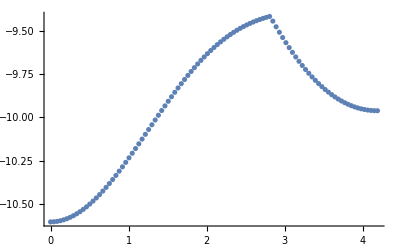

```mathematica
ListPlot[Table[{s vecL/3.,Sort[Eigenvalues[H[s vec/3.]]][[1]]},{s,0.,1.,0.01}]]
```

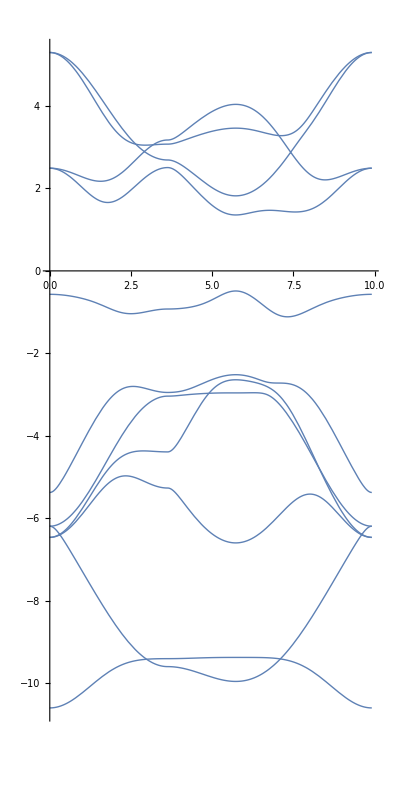

```mathematica
Plot[Sort[Eigenvalues[H[If[(vecL/3.+vecL/6.+2. π/√3.-s)<vecL/3.+vecL/6.,(vecL/3.+vecL/6.+2. π/√3.-s),vecL/3.+vecL/6.] vec/vecL+If[(vecL/3.+vecL/6.+2. π/√3.-s)<vecL/3.+vecL/6.,0.,(vecL/3.+vecL/6.+2. π/√3.-s)-(vecL/3.+vecL/6.)] vec1/vec1L]]//Re],{s,0.,vecL/3.+vecL/6.+2. π/√3.},AspectRatio->2,PlotStyle->Thick]
```

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

## Six orbital model

### Parameters

```mathematica
Δ0=-1.016;
Δ2=-2.529;
Δp=-0.780;
Δz=-7.740;
Vpds=-2.619;
Vpdp=-1.396;
Vdds=-0.933;
Vddp=-0.478;
Vddd=-0.442;
Vpps=0.696;
Vppp=0.278;
```

```mathematica
Clear[Δ0,Δ2,Δp,Δz,Vpds,Vpdp,Vdds,Vddp,Vddd,Vpps,Vppp];
```

### Hopping integrals

#### tpda

```mathematica
taxz2=(√2.)/(7. √7.)(√3. Vpds -9. Vpdp)
taxx2=(√2.)/(7. √7.)(3. Vpds+5. √3. Vpdp)
taxxy=-(√2.)/(7. √7.)(3. √3. Vpds+Vpdp)
```

0.0763604 (-9. Vpdp+1.73205 Vpds)

0.0763604 (8.66025 Vpdp+3. Vpds)

-0.0763604 (Vpdp+5.19615 Vpds)

```mathematica
tayz2=(√2.)/(7. √7.)(-Vpds+3. √3. Vpdp)
tayx2=(√2.)/(7. √7.)(-√3. Vpds+9. Vpdp)
tayxy=(√2.)/(7. √7.)(3. Vpds+5. √3. Vpdp)
```

0.0763604 (5.19615 Vpdp-Vpds)

0.0763604 (9. Vpdp-1.73205 Vpds)

0.0763604 (8.66025 Vpdp+3. Vpds)

```mathematica
tazz2=(√2.)/(7. √7.) (√3. Vpds+12. Vpdp)
tazx2=(√2.)/(7. √7.) (3. Vpds-2. √3. Vpdp)
tazxy=(√2.)/(7. √7.) (-3. √3. Vpds+6. Vpdp)
```

0.0763604 (12. Vpdp+1.73205 Vpds)

0.0763604 (-3.4641 Vpdp+3. Vpds)

0.0763604 (6. Vpdp-5.19615 Vpds)

#### tpdb

```mathematica
tbxz2=0.;
tbxx2=0.;
tbxxy=(2. √2.)/(√7.) Vpdp
```

1.06904 Vpdp

```mathematica
tbyz2=(√2.)/(7. √7.) (2. Vpds-6. √3. Vpdp)
tbyx2=-(√3. √2.)/(7. √7.) (4. Vpds+2. √3. Vpdp)
tbyxy=0.;
```

0.0763604 (-10.3923 Vpdp+2. Vpds)

-0.13226 (3.4641 Vpdp+4. Vpds)

```mathematica
tbzz2=(√2.)/(7. √7.) (√3. Vpds+12. Vpdp)
tbzx2=(√2.)/(7. √7.) (-6. Vpds+4. √3. Vpdp)
tbzxy=0.;
```

0.0763604 (12. Vpdp+1.73205 Vpds)

0.0763604 (6.9282 Vpdp-6. Vpds)

#### tpdg

```mathematica
tgxz2=-(√2.)/(7. √7.)(√3. Vpds -9. Vpdp)
tgxx2=-(√2.)/(7. √7.)(3. Vpds+5. √3. Vpdp)
tgxxy=-(√2.)/(7. √7.)(3. √3. Vpds+Vpdp)
```

-0.0763604 (-9. Vpdp+1.73205 Vpds)

-0.0763604 (8.66025 Vpdp+3. Vpds)

-0.0763604 (Vpdp+5.19615 Vpds)

```mathematica
tgyz2=(√2.)/(7. √7.)(-Vpds+3. √3. Vpdp)
tgyx2=(√2.)/(7. √7.)(-√3. Vpds+9. Vpdp)
tgyxy=-(√2.)/(7. √7.)(3. Vpds+5. √3. Vpdp)
```

0.0763604 (5.19615 Vpdp-Vpds)

0.0763604 (9. Vpdp-1.73205 Vpds)

-0.0763604 (8.66025 Vpdp+3. Vpds)

```mathematica
tgzz2=(√2.)/(7. √7.) (√3. Vpds+12. Vpdp)
tgzx2=(√2.)/(7. √7.) (3. Vpds-2. √3. Vpdp)
tgzxy=-(√2.)/(7. √7.) (-3. √3. Vpds+6. Vpdp)
```

0.0763604 (12. Vpdp+1.73205 Vpds)

0.0763604 (-3.4641 Vpdp+3. Vpds)

-0.0763604 (6. Vpdp-5.19615 Vpds)

#### tpp

```mathematica
taxx=1./4. (Vpps+3. Vppp)
taxy=(√3.)/4. (-Vpps+Vppp)
taxz=0.;
tayy=1./4. (3. Vpps+Vppp)
tayz=0.;
tazz=Vppp
```

0.25 (3. Vppp+Vpps)

0.433013 (Vppp-Vpps)

0.25 (Vppp+3. Vpps)

Vppp

```mathematica
tbxx=Vpps
tbyy=Vppp
tbzz=Vppp
```

Vpps

Vppp

Vppp

```mathematica
tgxx=1./4. (Vpps+3. Vppp)
tgxy=(√3.)/4. (Vpps-Vppp)
tgxz=0.;
tgyy=1./4. (3. Vpps+Vppp)
tgyz=0.;
tgzz=Vppp
```

0.25 (3. Vppp+Vpps)

0.433013 (-Vppp+Vpps)

0.25 (Vppp+3. Vpps)

Vppp

#### tdda

```mathematica
taz2z2=1./4.(Vdds +3. Vddd)
taz2x2=(√3.)/8.(Vdds-Vddd)
taz2xy=3./8.(Vdds-Vddd)
```

0.25 (3. Vddd+Vdds)

0.216506 (-Vddd+Vdds)

0.375 (-Vddd+Vdds)

```mathematica
tax2x2=1./16.(3. Vdds+12. Vddp+Vddd)
tax2xy=(√3.)/16.(3. Vdds-4. Vddp+Vddd)
```

0.0625 (Vddd+12. Vddp+3. Vdds)

0.108253 (Vddd-4. Vddp+3. Vdds)

```mathematica
taxyxy=1./16.(9. Vdds+4. Vddp+3.Vddd)
```

0.0625 (3. Vddd+4. Vddp+9. Vdds)

#### tddb

```mathematica
tbz2z2=1./4. (Vdds+3. Vddd)
tbz2x2=(√3.)/4. (-Vdds+Vddd)
tbz2xy=0.;
```

0.25 (3. Vddd+Vdds)

0.433013 (Vddd-Vdds)

```mathematica
tbx2x2=1./4. (3. Vdds+Vddd)
tbx2xy=0.;
```

0.25 (Vddd+3. Vdds)

```mathematica
tbxyxy=Vddp
```

Vddp

#### tddg

```mathematica
tgz2z2=1./4.(Vdds +3. Vddd)
tgz2x2=(√3.)/8.(Vdds-Vddd)
tgz2xy=3./8.(-Vdds+Vddd)
```

0.25 (3. Vddd+Vdds)

0.216506 (-Vddd+Vdds)

0.375 (Vddd-Vdds)

```mathematica
tgx2x2=1./16.(3. Vdds+12. Vddp+Vddd)
tgx2xy=(√3.)/16. (-3. Vdds+4. Vddp-Vddd)
```

0.0625 (Vddd+12. Vddp+3. Vdds)

0.108253 (-Vddd+4. Vddp-3. Vdds)

```mathematica
tgxyxy=1./16.(9. Vdds+4. Vddp+3.Vddd)
```

0.0625 (3. Vddd+4. Vddp+9. Vdds)

### Hamiltonian matrices

#### r, r

```mathematica
Hrr=Table[0.,{i,1,6},{j,1,6}];

Hrr[[1,1]]=Δ0;
Hrr[[2,2]]=Δ2;
Hrr[[3,3]]=Δ2;
Hrr[[4,4]]=Δp+Vppp;
Hrr[[5,5]]=Δp+Vppp;
Hrr[[6,6]]=Δz-Vpps;

Hrr[[1,4]]=taxz2;
Hrr[[1,5]]=tayz2;
Hrr[[1,6]]=tazz2;

Hrr[[2,4]]=taxx2;
Hrr[[2,5]]=tayx2;
Hrr[[2,6]]=tazx2;

Hrr[[3,4]]=taxxy;
Hrr[[3,5]]=tayxy;
Hrr[[3,6]]=tazxy;

For[i=2,i≤6,i++,
For[j=1,j<i,++j,
Hrr[[i,j]]=Hrr[[j,i]]
]
]
```

#### r, r+a1

```mathematica
Hrra1=Table[0.,{i,1,6},{j,1,6}];

Hrra1[[1,1]]=tbz2z2;
Hrra1[[1,2]]=tbz2x2;
Hrra1[[1,3]]=tbz2xy;

Hrra1[[1,4]]=tgxz2;
Hrra1[[1,5]]=tgyz2;
Hrra1[[1,6]]=tgzz2;

Hrra1[[2,1]]=tbz2x2;
Hrra1[[2,2]]=tbx2x2;
Hrra1[[2,3]]=tbx2xy;

Hrra1[[2,4]]=tgxx2;
Hrra1[[2,5]]=tgyx2;
Hrra1[[2,6]]=tgzx2;

Hrra1[[3,1]]=tbz2xy;
Hrra1[[3,2]]=tbx2xy;
Hrra1[[3,3]]=tbxyxy;

Hrra1[[3,4]]=tgxxy;
Hrra1[[3,5]]=tgyxy;
Hrra1[[3,6]]=tgzxy;

Hrra1[[4,4]]=tbxx;
Hrra1[[5,5]]=tbyy;
Hrra1[[6,6]]=tbzz;
```

#### r, r+a1-a2 && r, r-a1+a2

```mathematica
Hrra1a2=Table[0.,{i,1,6},{j,1,6}];

Hrra1a2[[1,1]]=tgz2z2;
Hrra1a2[[1,2]]=tgz2x2;
Hrra1a2[[1,3]]=tgz2xy;

Hrra1a2[[2,1]]=tgz2x2;
Hrra1a2[[2,2]]=tgx2x2;
Hrra1a2[[2,3]]=tgx2xy;

Hrra1a2[[3,1]]=tgz2xy;
Hrra1a2[[3,2]]=tgx2xy;
Hrra1a2[[3,3]]=tgxyxy;

Hrra1a2[[4,4]]=tgxx;
Hrra1a2[[4,5]]=tgxy;
Hrra1a2[[4,6]]=tgxz;

Hrra1a2[[5,4]]=tgxy;
Hrra1a2[[5,5]]=tgyy;
Hrra1a2[[5,6]]=tgyz;

Hrra1a2[[6,4]]=tgxz;
Hrra1a2[[6,5]]=tgyz;
Hrra1a2[[6,6]]=tgzz;
```

#### r, r-a2

```mathematica
Hrra2m=Table[0.,{i,1,6},{j,1,6}];

Hrra2m[[1,1]]=taz2z2;
Hrra2m[[1,2]]=taz2x2;
Hrra2m[[1,3]]=taz2xy;

Hrra2m[[2,1]]=taz2x2;
Hrra2m[[2,2]]=tax2x2;
Hrra2m[[2,3]]=tax2xy;

Hrra2m[[3,1]]=taz2xy;
Hrra2m[[3,2]]=tax2xy;
Hrra2m[[3,3]]=taxyxy;


Hrra2m[[4,4]]=taxx;
Hrra2m[[4,5]]=taxy;
Hrra2m[[4,6]]=taxz;

Hrra2m[[5,4]]=taxy;
Hrra2m[[5,5]]=tayy;
Hrra2m[[5,6]]=tayz;

Hrra2m[[6,4]]=taxz;
Hrra2m[[6,5]]=tayz;
Hrra2m[[6,6]]=tazz;


Hrra2m[[4,1]]=tbxz2;
Hrra2m[[4,2]]=tbxx2;
Hrra2m[[4,3]]=tbxxy;

Hrra2m[[5,1]]=tbyz2;
Hrra2m[[5,2]]=tbyx2;
Hrra2m[[5,3]]=tbyxy;

Hrra2m[[6,1]]=tbzz2;
Hrra2m[[6,2]]=tbzx2;
Hrra2m[[6,3]]=tbzxy;
```

#### r, r-a1

```mathematica
Hrra1m=Table[0.,{i,1,6},{j,1,6}];

Hrra1m[[1,1]]=tbz2z2;
Hrra1m[[1,2]]=tbz2x2;
Hrra1m[[1,3]]=tbz2xy;

Hrra1m[[2,1]]=tbz2x2;
Hrra1m[[2,2]]=tbx2x2;
Hrra1m[[2,3]]=tbx2xy;

Hrra1m[[3,1]]=tbz2xy;
Hrra1m[[3,2]]=tbx2xy;
Hrra1m[[3,3]]=tbxyxy;

Hrra1m[[4,4]]=tbxx;
Hrra1m[[5,5]]=tbyy;
Hrra1m[[6,6]]=tbzz;

Hrra1m[[4,1]]=tgxz2;
Hrra1m[[4,2]]=tgxx2;
Hrra1m[[4,3]]=tgxxy;

Hrra1m[[5,1]]=tgyz2;
Hrra1m[[5,2]]=tgyx2;
Hrra1m[[5,3]]=tgyxy;

Hrra1m[[6,1]]=tgzz2;
Hrra1m[[6,2]]=tgzx2;
Hrra1m[[6,3]]=tgzxy;
```

#### r, r+a2

```mathematica
Hrra2=Table[0.,{i,1,6},{j,1,6}];

Hrra2[[1,1]]=taz2z2;
Hrra2[[1,2]]=taz2x2;
Hrra2[[1,3]]=taz2xy;

Hrra2[[2,1]]=taz2x2;
Hrra2[[2,2]]=tax2x2;
Hrra2[[2,3]]=tax2xy;

Hrra2[[3,1]]=taz2xy;
Hrra2[[3,2]]=tax2xy;
Hrra2[[3,3]]=taxyxy;


Hrra2[[4,4]]=taxx;
Hrra2[[4,5]]=taxy;
Hrra2[[4,6]]=taxz;

Hrra2[[5,4]]=taxy;
Hrra2[[5,5]]=tayy;
Hrra2[[5,6]]=tayz;

Hrra2[[6,4]]=taxz;
Hrra2[[6,5]]=tayz;
Hrra2[[6,6]]=tazz;


Hrra2[[1,4]]=tbxz2;
Hrra2[[2,4]]=tbxx2;
Hrra2[[3,4]]=tbxxy;

Hrra2[[1,5]]=tbyz2;
Hrra2[[2,5]]=tbyx2;
Hrra2[[3,5]]=tbyxy;

Hrra2[[1,6]]=tbzz2;
Hrra2[[2,6]]=tbzx2;
Hrra2[[3,6]]=tbzxy;
```

### Hamiltonian k-sapce

#### Defenitions

```mathematica
a1={1,0};
a2={1./2.,(-√3.)/2.};
b1=2. π 2./(√3.){(√3.)/2.,1./2.};
b2=2. π 2./(√3.){0.,-1.};
```

#### Hamiltonian

```mathematica
H[k_]:=Hrr+Hrra1 ⅇ^(-ⅈ k.a1)+Hrra1m ⅇ^(ⅈ k.a1)+2. Cos[k.(a1-a2)] Hrra1a2+Hrra2m ⅇ^(ⅈ k.a2)+Hrra2 ⅇ^(-ⅈ k.a2);
```

### Spectrum

```mathematica
vec=b2+2. b1;
H[vec/3.]
```

{{(-0.75+0. ⅈ) (3. Vddd+Vdds)+Δ0,0.-(0.433013+0. ⅈ) (Vddd-Vdds)-(0.433013+0. ⅈ) (-Vddd+Vdds),(0.+0. ⅈ)-0.375 (Vddd-Vdds)-(0.375+0. ⅈ) (-Vddd+Vdds),(0.+0. ⅈ)+(0.114541-0.06613 ⅈ) (-9. Vpdp+1.73205 Vpds),(0.+0. ⅈ)+(0.0381802+0.06613 ⅈ) (5.19615 Vpdp-Vpds)-(0.0381802+0.06613 ⅈ) (-10.3923 Vpdp+2. Vpds),(0.+0. ⅈ)-(2.77556×10^-17+2.77556×10^-17 ⅈ) (12. Vpdp+1.73205 Vpds)},{0.-(0.433013+0. ⅈ) (Vddd-Vdds)-(0.433013+0. ⅈ) (-Vddd+Vdds),(-0.25+0. ⅈ) (Vddd+3. Vdds)-(0.125+0. ⅈ) (Vddd+12. Vddp+3. Vdds)+Δ2,(0.+0. ⅈ)-0.108253 (-Vddd+4. Vddp-3. Vdds)-(0.108253+0. ⅈ) (Vddd-4. Vddp+3. Vdds),(0.+0. ⅈ)+(0.114541-0.06613 ⅈ) (8.66025 Vpdp+3. Vpds),(0.+0. ⅈ)+(0.0381802+0.06613 ⅈ) (9. Vpdp-1.73205 Vpds)+(0.06613+0.114541 ⅈ) (3.4641 Vpdp+4. Vpds),(0.+0. ⅈ)-(0.0381802+0.06613 ⅈ) (6.9282 Vpdp-6. Vpds)+(0.0381802+0.06613 ⅈ) (-3.4641 Vpdp+3. Vpds)},{(0.+0. ⅈ)-0.375 (Vddd-Vdds)-(0.375+0. ⅈ) (-Vddd+Vdds),(0.+0. ⅈ)-0.108253 (-Vddd+4. Vddp-3. Vdds)-(0.108253+0. ⅈ) (Vddd-4. Vddp+3. Vdds),(-1.+0. ⅈ) Vddp-(0.125+0. ⅈ) (3. Vddd+4. Vddp+9. Vdds)+Δ2,(0.+0. ⅈ)-(0.534522+0.92582 ⅈ) Vpdp-(0.0381802+0.06613 ⅈ) (Vpdp+5.19615 Vpds),(0.+0. ⅈ)+(0.114541-0.06613 ⅈ) (8.66025 Vpdp+3. Vpds),(0.+0. ⅈ)+(0.114541-0.06613 ⅈ) (6. Vpdp-5.19615 Vpds)},{(0.+0. ⅈ)+(0.114541+0.06613 ⅈ) (-9. Vpdp+1.73205 Vpds),(0.+0. ⅈ)+(0.114541+0.06613 ⅈ) (8.66025 Vpdp+3. Vpds),(0.+0. ⅈ)-(0.534522-0.92582 ⅈ) Vpdp-(0.0381802-0.06613 ⅈ) (Vpdp+5.19615 Vpds),Vppp-(1.+0. ⅈ) Vpps-(0.5+0. ⅈ) (3. Vppp+Vpps)+Δp,(0.+0. ⅈ)-(0.433013+0. ⅈ) (Vppp-Vpps)-0.433013 (-Vppp+Vpps),0.+0. ⅈ},{(0.+0. ⅈ)+(0.0381802-0.06613 ⅈ) (5.19615 Vpdp-Vpds)-(0.0381802-0.06613 ⅈ) (-10.3923 Vpdp+2. Vpds),(0.+0. ⅈ)+(0.0381802-0.06613 ⅈ) (9. Vpdp-1.73205 Vpds)+(0.06613-0.114541 ⅈ) (3.4641 Vpdp+4. Vpds),(0.+0. ⅈ)+(0.114541+0.06613 ⅈ) (8.66025 Vpdp+3. Vpds),(0.+0. ⅈ)-(0.433013+0. ⅈ) (Vppp-Vpps)-0.433013 (-Vppp+Vpps),(-8.88178×10^-16+0. ⅈ) Vppp-(0.5+0. ⅈ) (Vppp+3. Vpps)+Δp,0.+0. ⅈ},{(0.+0. ⅈ)-(2.77556×10^-17-2.77556×10^-17 ⅈ) (12. Vpdp+1.73205 Vpds),(0.+0. ⅈ)-(0.0381802-0.06613 ⅈ) (6.9282 Vpdp-6. Vpds)+(0.0381802-0.06613 ⅈ) (-3.4641 Vpdp+3. Vpds),(0.+0. ⅈ)+(0.114541+0.06613 ⅈ) (6. Vpdp-5.19615 Vpds),0.+0. ⅈ,0.+0. ⅈ,(-3.+0. ⅈ) Vppp-Vpps+Δz}}

```mathematica
vec=b2+2. b1;
vecL=Sqrt[vec.vec];
vec1=b2/2.;
vec1L=Sqrt[vec1.vec1];
```

```mathematica
Eigenvalues[H[1. vec/3.]]
```

{Root[(-18.7301+8.88178×10^-16 ⅈ) Vpdp^6+1318+(3. Vddd+3. Vddp+3. Vdds+4. Vppp+4. Vpps-1. Δ0-2. Δ2-2. Δp-Δz) #1^5+#1^6&,1],Root[(-18.7301+8.88178×10^-16 ⅈ) Vpdp^6+1319+#1^6&,2],Root[1],1,Root[1&,5],Root[(-18.7301+8.88178×10^-16 ⅈ) Vpdp^6+1319+#1^6&,6]}
 |  |  |  |

```mathematica
Table[{s vecL/3.,Sort[Eigenvalues[H[s vec/3.]]][[1]]},{s,0.,1.,0.1}]
```

$Aborted

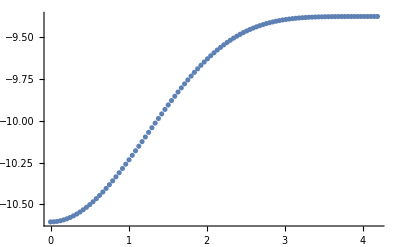

```mathematica
ListPlot[Table[{s vecL/3.,Sort[Eigenvalues[H[s vec/3.]]][[1]]},{s,0.,1.,0.01}]]
```

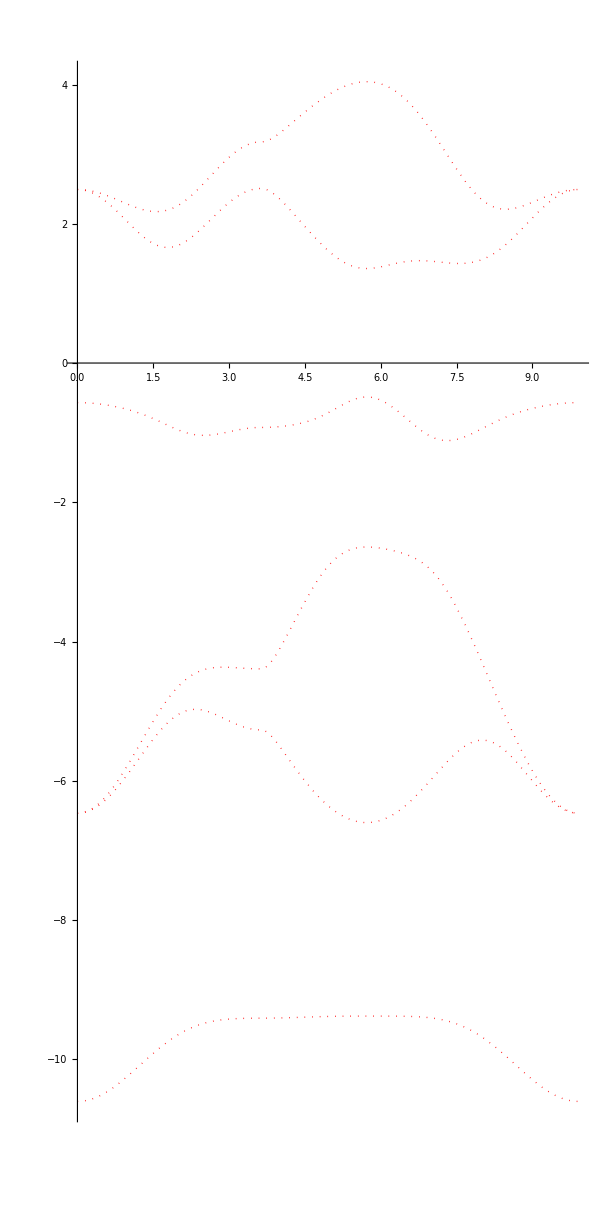

```mathematica
fig1=Plot[Sort[Eigenvalues[H[If[(vecL/3.+vecL/6.+2. π/√3.-s)<vecL/3.+vecL/6.,(vecL/3.+vecL/6.+2. π/√3.-s),vecL/3.+vecL/6.] vec/vecL+If[(vecL/3.+vecL/6.+2. π/√3.-s)<vecL/3.+vecL/6.,0.,(vecL/3.+vecL/6.+2. π/√3.-s)-(vecL/3.+vecL/6.)] vec1/vec1L]]//Re],{s,0.,vecL/3.+vecL/6.+2. π/√3.},AspectRatio->2,PlotStyle->{Thick,Red,Dotted}]
```

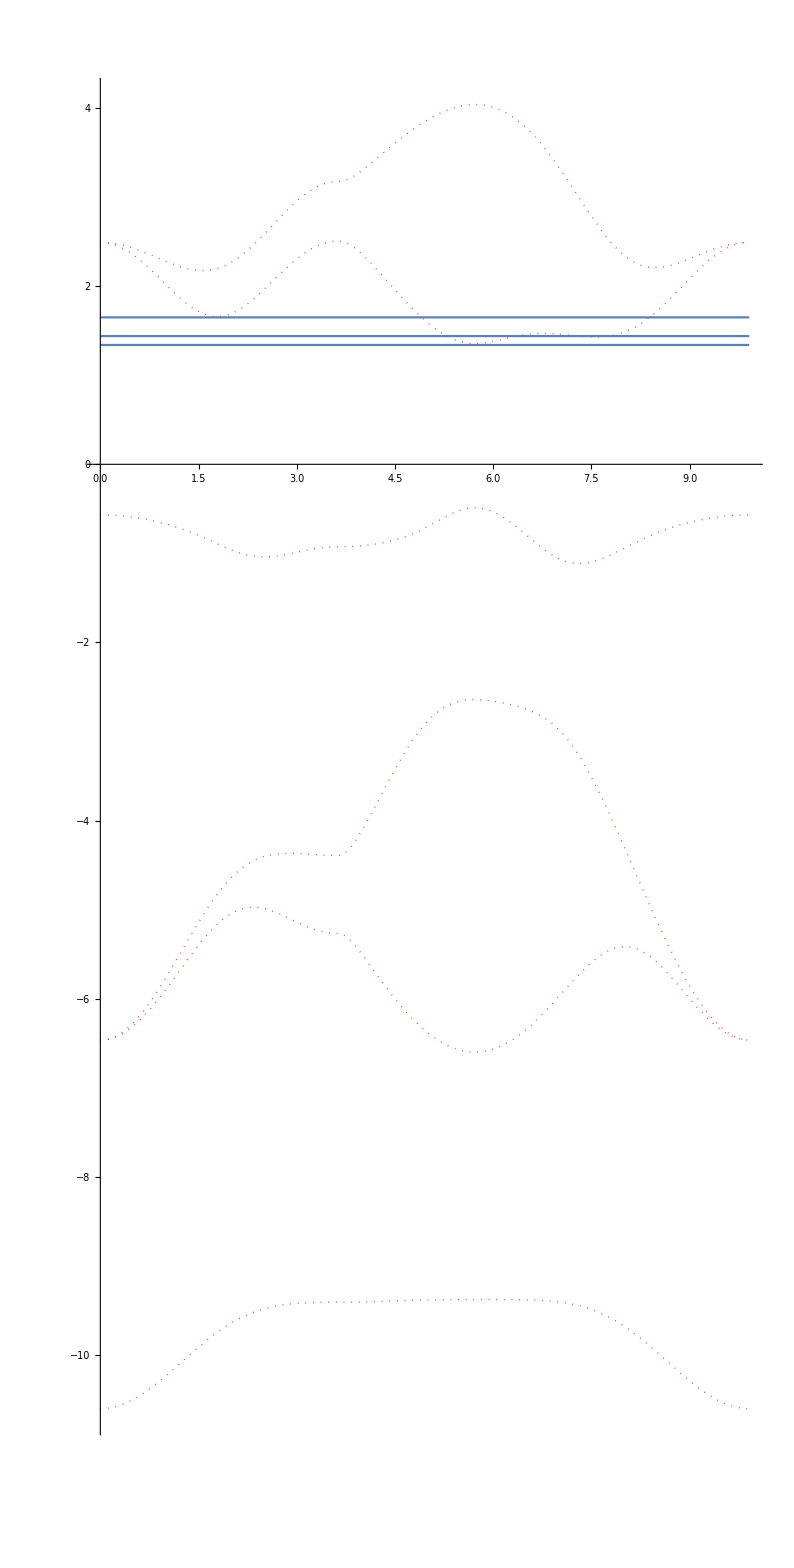

```mathematica
Show[{fig1,ListPlot[{{0.,1.34},{vecL/3.+vecL/6.+2. π/√3.,1.34}},Joined->True],ListPlot[{{0.,1.44},{vecL/3.+vecL/6.+2. π/√3.,1.44}},Joined->True],ListPlot[{{0.,1.65},{vecL/3.+vecL/6.+2. π/√3.,1.65}},Joined->True]}]
```

#### Analytic result at Gamma point

```mathematica
Γ0=Δ0+6*(Vdds+3. Vddd)/4.;
ΓzE=Δz+6.*Vppp-Vpps;
Γzd0=3./(7. √7.) (√3. Vpds+12. Vpdp);
(Γ0+ΓzE)/2.+√(((Γ0-ΓzE)/2.)^2+2. (Γzd0)^2)
```

-0.568376

### Filling density versus Fermi energy

```mathematica
occupation[ener_,Ek_]:=Module[{i=1,count=0.},While[i<=6&&Ek[[i]]<ener,++i];i-1];
filling[ener_,listE_,Ni_,Nj_]:=Table[occupation[ener,listE[[i,j]]],{i,1,Ni},{j,1,Nj}]//Flatten//Total;
```

```mathematica
NN=100;
NE=1000;
Emin=-11.;
Emax=5.;
listEigv=Table[Sort[Eigenvalues[H[i b1/NN+j b2/NN]]//Re],{i,1,NN},{j,1,NN}];
fillingVsE=Table[{EE=Emin+i (Emax-Emin)/NE;EE,filling[EE,listEigv,NN,NN]/(1.NN*NN)},{i,1,NE}];
```

```mathematica
fllingVsE={{-10.984,0},{-10.968,0},{-10.952,0},{-10.936,0},{-10.92,0},{-10.904,0},{-10.888,0},{-10.872,0},{-10.856,0},{-10.84,0},{-10.824,0},{-10.808,0},{-10.792,0},{-10.776,0},{-10.76,0},{-10.744,0},{-10.728,0},{-10.712,0},{-10.696,0},{-10.68,0},{-10.664,0},{-10.648,0},{-10.632,0},{-10.616,0},{-10.6,7/10000},{-10.584,37/10000},{-10.568,61/10000},{-10.552,17/2000},{-10.536,121/10000},{-10.52,139/10000},{-10.504,163/10000},{-10.488,199/10000},{-10.472,223/10000},{-10.456,253/10000},{-10.44,283/10000},{-10.424,313/10000},{-10.408,349/10000},{-10.392,367/10000},{-10.376,409/10000},{-10.36,433/10000},{-10.344,463/10000},{-10.328,499/10000},{-10.312,517/10000},{-10.296,559/10000},{-10.28,119/2000},{-10.264,637/10000},{-10.248,673/10000},{-10.232,703/10000},{-10.216,149/2000},{-10.2,769/10000},{-10.184,161/2000},{-10.168,847/10000},{-10.152,877/10000},{-10.136,37/400},{-10.12,191/2000},{-10.104,1003/10000},{-10.088,1039/10000},{-10.072,1069/10000},{-10.056,227/2000},{-10.04,1159/10000},{-10.024000000000001,1213/10000},{-10.008,1261/10000},{-9.992,257/2000},{-9.975999999999999,1369/10000},{-9.96,1393/10000},{-9.943999999999999,1459/10000},{-9.928,1507/10000},{-9.911999999999999,311/2000},{-9.896,323/2000},{-9.879999999999999,1663/10000},{-9.864,1723/10000},{-9.847999999999999,1777/10000},{-9.832,1813/10000},{-9.816,1891/10000},{-9.8,1957/10000},{-9.784,2041/10000},{-9.768,2083/10000},{-9.752,2161/10000},{-9.736,2233/10000},{-9.72,2323/10000},{-9.704,479/2000},{-9.688,2479/10000},{-9.672,103/400},{-9.656,533/2000},{-9.64,2761/10000},{-9.624,2857/10000},{-9.608,2953/10000},{-9.592,3091/10000},{-9.576,641/2000},{-9.56,3331/10000},{-9.544,3481/10000},{-9.528,3643/10000},{-9.512,3829/10000},{-9.496,4021/10000},{-9.48,4243/10000},{-9.464,4519/10000},{-9.448,971/2000},{-9.432,5269/10000},{-9.416,5911/10000},{-9.4,3779/5000},{-9.384,907/1000},{-9.368,1},{-9.352,1},{-9.336,1},{-9.32,1},{-9.304,1},{-9.288,1},{-9.272,1},{-9.256,1},{-9.24,1},{-9.224,1},{-9.208,1},{-9.192,1},{-9.176,1},{-9.16,1},{-9.144,1},{-9.128,1},{-9.112,1},{-9.096,1},{-9.08,1},{-9.064,1},{-9.048,1},{-9.032,1},{-9.016,1},{-9.,1},{-8.984,1},{-8.968,1},{-8.952,1},{-8.936,1},{-8.92,1},{-8.904,1},{-8.888,1},{-8.872,1},{-8.856,1},{-8.84,1},{-8.824,1},{-8.808,1},{-8.792,1},{-8.776,1},{-8.76,1},{-8.744,1},{-8.728,1},{-8.712,1},{-8.696,1},{-8.68,1},{-8.664,1},{-8.648,1},{-8.632,1},{-8.616,1},{-8.6,1},{-8.584,1},{-8.568,1},{-8.552,1},{-8.536,1},{-8.52,1},{-8.504,1},{-8.488,1},{-8.472,1},{-8.456,1},{-8.44,1},{-8.424,1},{-8.408,1},{-8.392,1},{-8.376,1},{-8.36,1},{-8.344,1},{-8.328,1},{-8.312,1},{-8.296,1},{-8.28,1},{-8.264,1},{-8.248,1},{-8.232,1},{-8.216,1},{-8.2,1},{-8.184000000000001,1},{-8.168,1},{-8.152000000000001,1},{-8.136,1},{-8.120000000000001,1},{-8.104,1},{-8.088000000000001,1},{-8.072,1},{-8.056000000000001,1},{-8.04,1},{-8.024000000000001,1},{-8.008,1},{-7.992,1},{-7.976,1},{-7.96,1},{-7.944,1},{-7.928,1},{-7.912,1},{-7.896,1},{-7.88,1},{-7.864,1},{-7.848,1},{-7.832,1},{-7.816,1},{-7.8,1},{-7.784,1},{-7.768,1},{-7.752,1},{-7.736,1},{-7.72,1},{-7.704,1},{-7.688,1},{-7.672,1},{-7.656000000000001,1},{-7.640000000000001,1},{-7.6240000000000006,1},{-7.6080000000000005,1},{-7.5920000000000005,1},{-7.5760000000000005,1},{-7.5600000000000005,1},{-7.5440000000000005,1},{-7.5280000000000005,1},{-7.5120000000000005,1},{-7.496,1},{-7.48,1},{-7.464,1},{-7.448,1},{-7.432,1},{-7.416,1},{-7.4,1},{-7.384,1},{-7.368,1},{-7.352,1},{-7.336,1},{-7.32,1},{-7.304,1},{-7.288,1},{-7.272,1},{-7.256,1},{-7.24,1},{-7.224,1},{-7.208,1},{-7.192,1},{-7.176,1},{-7.16,1},{-7.144,1},{-7.128,1},{-7.112,1},{-7.096,1},{-7.08,1},{-7.064,1},{-7.048,1},{-7.032,1},{-7.016,1},{-7.,1},{-6.984,1},{-6.968,1},{-6.952,1},{-6.936,1},{-6.92,1},{-6.904,1},{-6.888,1},{-6.872,1},{-6.856,1},{-6.84,1},{-6.824,1},{-6.808,1},{-6.792,1},{-6.776,1},{-6.76,1},{-6.744,1},{-6.728,1},{-6.712,1},{-6.696,1},{-6.68,1},{-6.664,1},{-6.648,1},{-6.632,1},{-6.616,1},{-6.6,1},{-6.584,5027/5000},{-6.568,2527/2500},{-6.552,2539/2500},{-6.536,2551/2500},{-6.52,5129/5000},{-6.504,1289/1250},{-6.4879999999999995,2593/2500},{-6.4719999999999995,5213/5000},{-6.4559999999999995,2619/2500},{-6.4399999999999995,1059/1000},{-6.4239999999999995,2661/2500},{-6.4079999999999995,5379/5000},{-6.3919999999999995,2709/2500},{-6.376,5469/5000},{-6.36,2751/2500},{-6.344,111/100},{-6.328,1119/1000},{-6.312,1407/1250},{-6.296,1137/1000},{-6.28,5727/5000},{-6.264,5763/5000},{-6.248,5823/5000},{-6.232,5859/5000},{-6.216,5901/5000},{-6.2,5961/5000},{-6.184,5991/5000},{-6.168,6039/5000},{-6.152,6093/5000},{-6.136,1227/1000},{-6.12,3087/2500},{-6.104,6231/5000},{-6.088,6279/5000},{-6.072,6327/5000},{-6.056,798/625},{-6.04,3213/2500},{-6.024,3243/2500},{-6.008,816/625},{-5.992,6579/5000},{-5.976,6621/5000},{-5.96,3339/2500},{-5.944,1347/1000},{-5.928,6783/5000},{-5.912,273/200},{-5.896,6879/5000},{-5.88,1737/1250},{-5.864,699/500},{-5.848,7047/5000},{-5.832,3543/2500},{-5.816,3579/2500},{-5.8,903/625},{-5.784,909/625},{-5.768,3657/2500},{-5.752,3693/2500},{-5.736,3723/2500},{-5.72,7503/5000},{-5.704,1887/1250},{-5.688,3819/2500},{-5.672,3843/2500},{-5.656,7737/5000},{-5.64,1563/1000},{-5.624,3939/2500},{-5.608,7959/5000},{-5.592,8019/5000},{-5.576,8073/5000},{-5.56,8151/5000},{-5.544,8229/5000},{-5.528,1038/625},{-5.512,8373/5000},{-5.4959999999999996,8463/5000},{-5.4799999999999995,1707/1000},{-5.4639999999999995,8637/5000},{-5.4479999999999995,2181/1250},{-5.4319999999999995,8829/5000},{-5.4159999999999995,1119/625},{-5.3999999999999995,4539/2500},{-5.3839999999999995,9189/5000},{-5.368,927/500},{-5.352,234/125},{-5.336,4731/2500},{-5.32,1194/625},{-5.304,9603/5000},{-5.288,9693/5000},{-5.272,9789/5000},{-5.256,19749/10000},{-5.24,19917/10000},{-5.224,4011/2000},{-5.208,20193/10000},{-5.192,4059/2000},{-5.176,20451/10000},{-5.16,20583/10000},{-5.144,20667/10000},{-5.128,4161/2000},{-5.112,4179/2000},{-5.096,20967/10000},{-5.08,843/400},{-5.064,21189/10000},{-5.048,21321/10000},{-5.032,21387/10000},{-5.016,21459/10000},{-5.,21543/10000},{-4.984,21591/10000},{-4.968,21693/10000},{-4.952,21741/10000},{-4.936,21771/10000},{-4.92,21783/10000},{-4.904,21783/10000},{-4.888,4359/2000},{-4.872,4359/2000},{-4.856,21909/10000},{-4.84,21933/10000},{-4.824,4389/2000},{-4.808,4389/2000},{-4.792,21951/10000},{-4.776,21987/10000},{-4.76,22089/10000},{-4.744,22101/10000},{-4.728,22107/10000},{-4.712,22107/10000},{-4.696,22143/10000},{-4.68,22179/10000},{-4.664,22233/10000},{-4.648,22269/10000},{-4.632,4461/2000},{-4.616,22323/10000},{-4.6,22347/10000},{-4.584,22359/10000},{-4.568,897/400},{-4.552,4497/2000},{-4.536,4503/2000},{-4.52,4509/2000},{-4.504,22569/10000},{-4.4879999999999995,22611/10000},{-4.4719999999999995,22647/10000},{-4.4559999999999995,22701/10000},{-4.4399999999999995,22773/10000},{-4.4239999999999995,4563/2000},{-4.4079999999999995,22869/10000},{-4.3919999999999995,11451/5000},{-4.3759999999999994,11529/5000},{-4.359999999999999,11601/5000},{-4.343999999999999,5847/2500},{-4.328,11751/5000},{-4.312,11793/5000},{-4.296,2367/1000},{-4.28,11883/5000},{-4.264,11931/5000},{-4.248,11949/5000},{-4.232,3003/1250},{-4.216,603/250},{-4.2,1512/625},{-4.184,3027/1250},{-4.168,243/100},{-4.152,1524/625},{-4.136,6123/2500},{-4.12,12279/5000},{-4.104,12279/5000},{-4.088,1233/500},{-4.072,3093/1250},{-4.056,1551/625},{-4.04,621/250},{-4.024,1557/625},{-4.008,3123/1250},{-3.992,6267/2500},{-3.976,1572/625},{-3.96,3147/1250},{-3.944,6303/2500},{-3.928,2529/1000},{-3.912,1269/500},{-3.896,3183/1250},{-3.88,51/20},{-3.864,3189/1250},{-3.848,1596/625},{-3.832,3207/1250},{-3.816,3219/1250},{-3.8,129/50},{-3.784,1614/625},{-3.768,3231/1250},{-3.752,12957/5000},{-3.7359999999999998,12999/5000},{-3.7199999999999998,261/100},{-3.7039999999999997,6531/2500},{-3.6879999999999997,6531/2500},{-3.6719999999999997,3273/1250},{-3.6559999999999997,1641/625},{-3.6399999999999997,6597/2500},{-3.6239999999999997,6603/2500},{-3.6079999999999997,3303/1250},{-3.5919999999999996,1653/625},{-3.5759999999999996,531/200},{-3.5599999999999996,13299/5000},{-3.5439999999999996,13341/5000},{-3.5279999999999996,3339/1250},{-3.5119999999999996,6681/2500},{-3.4959999999999996,1674/625},{-3.4799999999999995,6717/2500},{-3.4639999999999995,3369/1250},{-3.4479999999999995,6747/2500},{-3.4319999999999995,6753/2500},{-3.4159999999999995,2703/1000},{-3.3999999999999995,13563/5000},{-3.3839999999999995,13611/5000},{-3.3679999999999994,6813/2500},{-3.3519999999999994,1704/625},{-3.3359999999999994,3411/1250},{-3.3200000000000003,6843/2500},{-3.3040000000000003,6873/2500},{-3.2880000000000003,1719/625},{-3.2720000000000002,3441/1250},{-3.2560000000000002,13779/5000},{-3.24,13821/5000},{-3.224,6939/2500},{-3.208,6939/2500},{-3.192,1389/500},{-3.176,348/125},{-3.16,1746/625},{-3.144,6999/2500},{-3.128,3501/1250},{-3.112,1401/500},{-3.096,1407/500},{-3.08,7053/2500},{-3.064,1764/625},{-3.048,3531/1250},{-3.032,7089/2500},{-3.016,7107/2500},{-3.,711/250},{-2.984,2847/1000},{-2.968,7149/2500},{-2.952,7161/2500},{-2.936,7167/2500},{-2.92,1437/500},{-2.904,14421/5000},{-2.888,14427/5000},{-2.872,7233/2500},{-2.856,3627/1250},{-2.84,14523/5000},{-2.824,14589/5000},{-2.808,14601/5000},{-2.792,7311/2500},{-2.776,14673/5000},{-2.76,14697/5000},{-2.7439999999999998,3687/1250},{-2.7279999999999998,7389/2500},{-2.7119999999999997,741/250},{-2.6959999999999997,2973/1000},{-2.6799999999999997,1491/500},{-2.6639999999999997,14943/5000},{-2.6479999999999997,3747/1250},{-2.6319999999999997,3},{-2.6159999999999997,3},{-2.5999999999999996,3},{-2.5839999999999996,3},{-2.5679999999999996,3},{-2.5519999999999996,3},{-2.5359999999999996,3},{-2.5199999999999996,3},{-2.5039999999999996,3},{-2.4879999999999995,3},{-2.4719999999999995,3},{-2.4559999999999995,3},{-2.4399999999999995,3},{-2.4239999999999995,3},{-2.4079999999999995,3},{-2.3919999999999995,3},{-2.3759999999999994,3},{-2.3599999999999994,3},{-2.3439999999999994,3},{-2.3279999999999994,3},{-2.3119999999999994,3},{-2.2959999999999994,3},{-2.2799999999999994,3},{-2.2639999999999993,3},{-2.2479999999999993,3},{-2.2319999999999993,3},{-2.2159999999999993,3},{-2.1999999999999993,3},{-2.1839999999999993,3},{-2.1679999999999993,3},{-2.1519999999999992,3},{-2.1359999999999992,3},{-2.119999999999999,3},{-2.103999999999999,3},{-2.087999999999999,3},{-2.071999999999999,3},{-2.055999999999999,3},{-2.039999999999999,3},{-2.023999999999999,3},{-2.007999999999999,3},{-1.991999999999999,3},{-1.975999999999999,3},{-1.959999999999999,3},{-1.943999999999999,3},{-1.927999999999999,3},{-1.911999999999999,3},{-1.895999999999999,3},{-1.879999999999999,3},{-1.863999999999999,3},{-1.847999999999999,3},{-1.831999999999999,3},{-1.815999999999999,3},{-1.799999999999999,3},{-1.783999999999999,3},{-1.7680000000000007,3},{-1.7520000000000007,3},{-1.7360000000000007,3},{-1.7200000000000006,3},{-1.7040000000000006,3},{-1.6880000000000006,3},{-1.6720000000000006,3},{-1.6560000000000006,3},{-1.6400000000000006,3},{-1.6240000000000006,3},{-1.6080000000000005,3},{-1.5920000000000005,3},{-1.5760000000000005,3},{-1.5600000000000005,3},{-1.5440000000000005,3},{-1.5280000000000005,3},{-1.5120000000000005,3},{-1.4960000000000004,3},{-1.4800000000000004,3},{-1.4640000000000004,3},{-1.4480000000000004,3},{-1.4320000000000004,3},{-1.4160000000000004,3},{-1.4000000000000004,3},{-1.3840000000000003,3},{-1.3680000000000003,3},{-1.3520000000000003,3},{-1.3360000000000003,3},{-1.3200000000000003,3},{-1.3040000000000003,3},{-1.2880000000000003,3},{-1.2720000000000002,3},{-1.2560000000000002,3},{-1.2400000000000002,3},{-1.2240000000000002,3},{-1.2080000000000002,3},{-1.1920000000000002,3},{-1.1760000000000002,3},{-1.1600000000000001,3},{-1.1440000000000001,3},{-1.1280000000000001,3},{-1.112,15021/5000},{-1.096,15141/5000},{-1.08,3819/1250},{-1.064,15441/5000},{-1.048,1956/625},{-1.032,801/250},{-1.016,3261/1000},{-1.,16551/5000},{-0.984,16749/5000},{-0.968,16953/5000},{-0.952,4287/1250},{-0.9359999999999999,2172/625},{-0.9199999999999999,35283/10000},{-0.9039999999999999,1431/400},{-0.8879999999999999,36009/10000},{-0.8719999999999999,36327/10000},{-0.8559999999999999,36549/10000},{-0.8399999999999999,36843/10000},{-0.8239999999999998,7401/2000},{-0.8079999999999998,7443/2000},{-0.7919999999999998,1497/400},{-0.7759999999999998,37617/10000},{-0.7599999999999998,7569/2000},{-0.7439999999999998,37989/10000},{-0.7279999999999998,7629/2000},{-0.7119999999999997,38343/10000},{-0.6959999999999997,38511/10000},{-0.6799999999999997,38691/10000},{-0.6639999999999997,38859/10000},{-0.6479999999999997,7803/2000},{-0.6319999999999997,39171/10000},{-0.6159999999999997,39363/10000},{-0.5999999999999996,39489/10000},{-0.5839999999999996,39651/10000},{-0.5679999999999996,9949/2500},{-0.5519999999999996,4979/1250},{-0.5359999999999996,997/250},{-0.5199999999999996,9979/2500},{-0.5039999999999996,9991/2500},{-0.48799999999999955,4},{-0.47199999999999953,4},{-0.4559999999999995,4},{-0.4399999999999995,4},{-0.4239999999999995,4},{-0.4079999999999995,4},{-0.39199999999999946,4},{-0.37599999999999945,4},{-0.35999999999999943,4},{-0.3439999999999994,4},{-0.3279999999999994,4},{-0.3119999999999994,4},{-0.2959999999999994,4},{-0.27999999999999936,4},{-0.26399999999999935,4},{-0.24799999999999933,4},{-0.23199999999999932,4},{-0.2159999999999993,4},{-0.1999999999999993,4},{-0.18399999999999928,4},{-0.16799999999999926,4},{-0.15199999999999925,4},{-0.13599999999999923,4},{-0.11999999999999922,4},{-0.1039999999999992,4},{-0.08799999999999919,4},{-0.07199999999999918,4},{-0.05599999999999916,4},{-0.03999999999999915,4},{-0.023999999999999133,4},{-0.007999999999999119,4},{0.008000000000000895,4},{0.02400000000000091,4},{0.040000000000000924,4},{0.05600000000000094,4},{0.07200000000000095,4},{0.08800000000000097,4},{0.10400000000000098,4},{0.120000000000001,4},{0.136000000000001,4},{0.15200000000000102,4},{0.16800000000000104,4},{0.18400000000000105,4},{0.20000000000000107,4},{0.21600000000000108,4},{0.2320000000000011,4},{0.2480000000000011,4},{0.26399999999999935,4},{0.27999999999999936,4},{0.2959999999999994,4},{0.3119999999999994,4},{0.3279999999999994,4},{0.3439999999999994,4},{0.35999999999999943,4},{0.37599999999999945,4},{0.39199999999999946,4},{0.4079999999999995,4},{0.4239999999999995,4},{0.4399999999999995,4},{0.4559999999999995,4},{0.47199999999999953,4},{0.48799999999999955,4},{0.5039999999999996,4},{0.5199999999999996,4},{0.5359999999999996,4},{0.5519999999999996,4},{0.5679999999999996,4},{0.5839999999999996,4},{0.5999999999999996,4},{0.6159999999999997,4},{0.6319999999999997,4},{0.6479999999999997,4},{0.6639999999999997,4},{0.6799999999999997,4},{0.6959999999999997,4},{0.7119999999999997,4},{0.7279999999999998,4},{0.7439999999999998,4},{0.7599999999999998,4},{0.7759999999999998,4},{0.7919999999999998,4},{0.8079999999999998,4},{0.8239999999999998,4},{0.8399999999999999,4},{0.8559999999999999,4},{0.8719999999999999,4},{0.8879999999999999,4},{0.9039999999999999,4},{0.9199999999999999,4},{0.9359999999999999,4},{0.952,4},{0.968,4},{0.984,4},{1.,4},{1.016,4},{1.032,4},{1.048,4},{1.064,4},{1.08,4},{1.096,4},{1.112,4},{1.1280000000000001,4},{1.1440000000000001,4},{1.1600000000000001,4},{1.1760000000000002,4},{1.1920000000000002,4},{1.2080000000000002,4},{1.2240000000000002,4},{1.2400000000000002,4},{1.2560000000000002,4},{1.2720000000000002,4},{1.2880000000000003,4},{1.3040000000000003,4},{1.3200000000000003,4},{1.3360000000000003,4},{1.3520000000000003,4},{1.3680000000000003,20021/5000},{1.3840000000000003,20051/5000},{1.4000000000000004,20081/5000},{1.4160000000000004,20117/5000},{1.4320000000000004,1009/250},{1.4480000000000004,10159/2500},{1.4640000000000004,20477/5000},{1.4800000000000004,518/125},{1.4960000000000004,20849/5000},{1.5120000000000005,2099/500},{1.5280000000000005,2638/625},{1.5440000000000005,21239/5000},{1.5600000000000005,21347/5000},{1.5760000000000005,21473/5000},{1.5920000000000005,21587/5000},{1.6080000000000005,21719/5000},{1.6240000000000006,21851/5000},{1.6400000000000006,21959/5000},{1.6560000000000006,22079/5000},{1.6720000000000006,22271/5000},{1.6880000000000006,22349/5000},{1.7040000000000006,2812/625},{1.7200000000000006,22577/5000},{1.7360000000000007,5669/1250},{1.7520000000000007,11377/2500},{1.7680000000000007,5711/1250},{1.7840000000000007,22931/5000},{1.8000000000000007,4603/1000},{1.8160000000000007,23069/5000},{1.8320000000000007,2893/625},{1.8480000000000008,23219/5000},{1.8640000000000008,4657/1000},{1.8800000000000008,4669/1000},{1.8960000000000008,2926/625},{1.9120000000000008,23471/5000},{1.9280000000000008,2941/625},{1.9440000000000008,4717/1000},{1.9600000000000009,23639/5000},{1.9760000000000009,23687/5000},{1.9920000000000009,5939/1250},{2.008000000000001,5951/1250},{2.024000000000001,5963/1250},{2.040000000000001,11953/2500},{2.056000000000001,23951/5000},{2.072000000000001,23993/5000},{2.088000000000001,24047/5000},{2.104000000000001,602/125},{2.120000000000001,12067/2500},{2.136000000000001,3022/625},{2.152000000000001,24227/5000},{2.168000000000001,3034/625},{2.184000000000001,24377/5000},{2.200000000000001,24581/5000},{2.216000000000001,24833/5000},{2.232000000000001,6257/1250},{2.248000000000001,629/125},{2.264000000000001,2531/500},{2.280000000000001,5083/1000},{2.296000000000001,25547/5000},{2.312000000000001,25643/5000},{2.3279999999999994,644/125},{2.3439999999999994,25859/5000},{2.3599999999999994,2597/500},{2.3759999999999994,13033/2500},{2.3919999999999995,13069/2500},{2.4079999999999995,6563/1250},{2.4239999999999995,26333/5000},{2.4399999999999995,26393/5000},{2.4559999999999995,26507/5000},{2.4719999999999995,13297/2500},{2.4879999999999995,13327/2500},{2.5039999999999996,6681/1250},{2.5199999999999996,53553/10000},{2.5359999999999996,10713/2000},{2.5519999999999996,429/80},{2.5679999999999996,10743/2000},{2.5839999999999996,53763/10000},{2.5999999999999996,2151/400},{2.6159999999999997,53877/10000},{2.6319999999999997,53979/10000},{2.6479999999999997,53991/10000},{2.6639999999999997,10803/2000},{2.6799999999999997,10821/2000},{2.6959999999999997,54201/10000},{2.7119999999999997,54213/10000},{2.7279999999999998,54267/10000},{2.7439999999999998,54339/10000},{2.76,54423/10000},{2.776,54441/10000},{2.792,54519/10000},{2.808,54567/10000},{2.824,54627/10000},{2.84,54681/10000},{2.856,10953/2000},{2.872,54813/10000},{2.888,54849/10000},{2.904,54969/10000},{2.92,55017/10000},{2.936,55053/10000},{2.952,55107/10000},{2.968,55251/10000},{2.984,2211/400},{3.,55317/10000},{3.016,55401/10000},{3.032,55467/10000},{3.048,55569/10000},{3.064,55617/10000},{3.08,55671/10000},{3.096,55767/10000},{3.112,55881/10000},{3.128,55947/10000},{3.144,56031/10000},{3.16,56097/10000},{3.176,14061/2500},{3.192,5637/1000},{3.208,3528/625},{3.224,1413/250},{3.24,28317/5000},{3.2560000000000002,28371/5000},{3.2720000000000002,28407/5000},{3.2880000000000003,28443/5000},{3.3040000000000003,3561/625},{3.3200000000000003,28527/5000},{3.3360000000000003,28569/5000},{3.3520000000000003,28599/5000},{3.3680000000000003,5727/1000},{3.3840000000000003,7173/1250},{3.4000000000000004,2871/500},{3.4160000000000004,3594/625},{3.4320000000000004,14391/2500},{3.4480000000000004,28833/5000},{3.4640000000000004,14433/2500},{3.4800000000000004,7221/1250},{3.4960000000000004,14463/2500},{3.5120000000000005,14487/2500},{3.5280000000000005,14499/2500},{3.5440000000000005,29031/5000},{3.5600000000000005,29067/5000},{3.5760000000000005,14553/2500},{3.5920000000000005,2913/500},{3.6080000000000005,729/125},{3.6240000000000006,5841/1000},{3.6400000000000006,5847/1000},{3.6560000000000006,29259/5000},{3.6720000000000006,29301/5000},{3.6880000000000006,29337/5000},{3.7040000000000006,29361/5000},{3.7200000000000006,29397/5000},{3.7360000000000007,29427/5000},{3.7520000000000007,14733/2500},{3.7680000000000007,3687/625},{3.7840000000000007,29523/5000},{3.8000000000000007,29547/5000},{3.8160000000000007,3699/625},{3.8320000000000007,3702/625},{3.8480000000000008,14823/2500},{3.8640000000000008,29673/5000},{3.880000000000001,297/50},{3.896000000000001,3717/625},{3.912000000000001,744/125},{3.928000000000001,7449/1250},{3.944000000000001,3729/625},{3.960000000000001,597/100},{3.976000000000001,747/125},{3.992000000000001,7479/1250},{4.008000000000001,1497/250},{4.024000000000001,2997/500},{4.040000000000001,6},{4.056000000000001,6},{4.072000000000001,6},{4.088000000000001,6},{4.104000000000001,6},{4.120000000000001,6},{4.136000000000001,6},{4.152000000000001,6},{4.168000000000001,6},{4.184000000000001,6},{4.200000000000001,6},{4.216000000000001,6},{4.232000000000001,6},{4.248000000000001,6},{4.264000000000001,6},{4.280000000000001,6},{4.296000000000001,6},{4.312000000000001,6},{4.328000000000001,6},{4.344000000000001,6},{4.359999999999999,6},{4.3759999999999994,6},{4.3919999999999995,6},{4.4079999999999995,6},{4.4239999999999995,6},{4.4399999999999995,6},{4.4559999999999995,6},{4.4719999999999995,6},{4.4879999999999995,6},{4.504,6},{4.52,6},{4.536,6},{4.552,6},{4.568,6},{4.584,6},{4.6,6},{4.616,6},{4.632,6},{4.648,6},{4.664,6},{4.68,6},{4.696,6},{4.712,6},{4.728,6},{4.744,6},{4.76,6},{4.776,6},{4.792,6},{4.808,6},{4.824,6},{4.84,6},{4.856,6},{4.872,6},{4.888,6},{4.904,6},{4.92,6},{4.936,6},{4.952,6},{4.968,6},{4.984,6},{5.,6}};
```

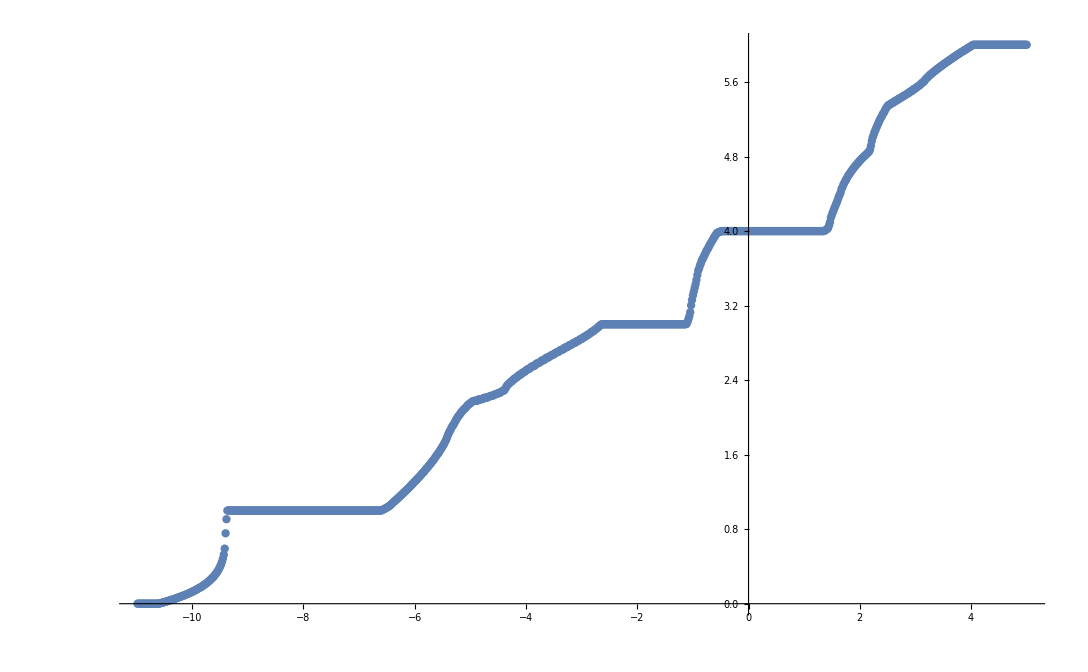

```mathematica
ListPlot[fllingVsE]
```

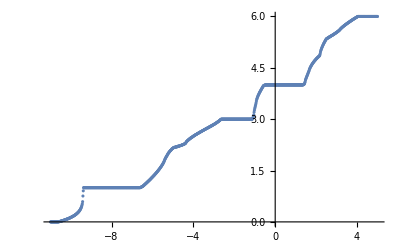

```mathematica
ListPlot[fillingVsE]
```

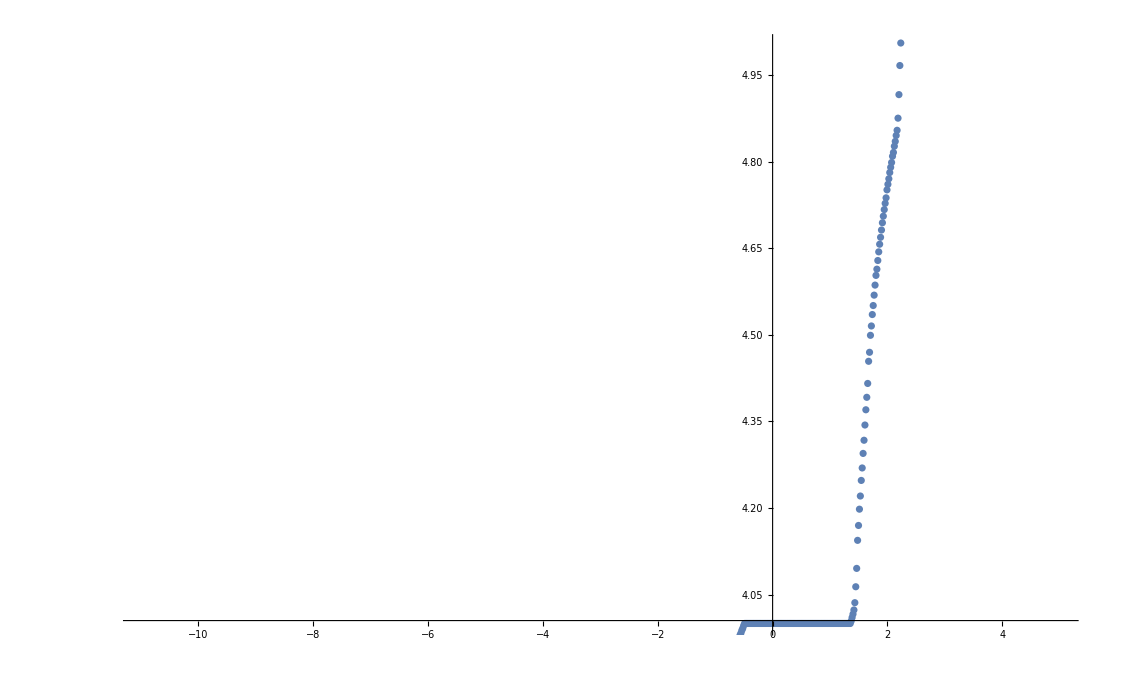

```mathematica
ListPlot[fllingVsE,PlotRange->{4.,5.}]
```

```mathematica
Export["filling-MoS2-6band.dat",Flatten[{fillingVsE,""},1]]
```

filling-MoS2-6band.dat

NOTE: The analysis (also xmgr) shows that the energy difference from bottom of conduction band (at K, K’) to the local minima at Q poits is ~0.01eV, which translates into 0.1 electron/unit cell, and which implies an electron density ~10^14 cm^-2.

## Seven orbital model

### Parameters

```mathematica
Δ0=-1.45;
Δ2=-5.8;
Δp=5.53;
Vpds=0.398;
Vpdp=-2.00;
```

### Hopping integrals

#### tpda

```mathematica
taxpz2=(√3.-ⅈ)/(7. √7. √2.)(Vpds -3. √3. Vpdp);
taxmz2=(√3.+ⅈ)/(7. √7. √2.)(Vpds -3. √3. Vpdp);
taxpx2=1./(7. √7.)(-ⅈ 2. √3. Vpds+ⅈ 4. Vpdp);
taxmx2=(√3.-ⅈ)/(7. √7.)(√3. Vpds +5. Vpdp);
taxpx2m=(√3.+ⅈ)/(7. √7.)(√3. Vpds +5. Vpdp);
taxmx2m=-1./(7. √7.)(-ⅈ 2. √3. Vpds+ⅈ 4. Vpdp);
```

#### tpdb

```mathematica
tbxpz2=ⅈ/(7. √7. √2.)(2. Vpds -6. √3. Vpdp);
tbxmz2=-ⅈ/(7. √7. √2.)(2. Vpds -6. √3. Vpdp);
tbxpx2=-ⅈ/(7. √7.)(2. √3. Vpds-4. Vpdp);
tbxmx2=ⅈ/(7. √7.)(2. √3. Vpds+10. Vpdp);
tbxpx2m=-ⅈ/(7. √7.)(2. √3. Vpds+10. Vpdp);
tbxmx2m=ⅈ/(7. √7.)(2. √3. Vpds-4. Vpdp);
```

#### tpdg

```mathematica
tgxpz2=(-(√3.+ⅈ))/(7. √7. √2.)(Vpds -3. √3. Vpdp);
tgxmz2=(-(√3.-ⅈ))/(7. √7. √2.)(Vpds -3. √3. Vpdp);
tgxpx2=1./(7. √7.)(-ⅈ 2. √3. Vpds+ⅈ 4. Vpdp);
tgxmx2=(-(√3.+ⅈ))/(7. √7.)(√3. Vpds +5. Vpdp);
tgxpx2m=(-(√3.-ⅈ))/(7. √7.)(√3. Vpds +5. Vpdp);
tgxmx2m=-1./(7. √7.)(-ⅈ 2. √3. Vpds+ⅈ 4. Vpdp);
```

### Hamiltonian matrices

#### r, r

```mathematica
Hrr=Table[0.,{i,1,7},{j,1,7}];

Hrr[[1,1]]=Δ0;
Hrr[[2,2]]=Δ2;
Hrr[[3,3]]=Δ2;
Hrr[[4,4]]=Δp;
Hrr[[5,5]]=Δp;
Hrr[[6,6]]=Δp;
Hrr[[7,7]]=Δp;

Hrr[[1,4]]=taxpz2;
Hrr[[1,5]]=taxmz2;
Hrr[[1,6]]=taxpz2;
Hrr[[1,7]]=taxmz2;

Hrr[[2,4]]=taxpx2;
Hrr[[2,5]]=taxmx2;
Hrr[[2,6]]=taxpx2;
Hrr[[2,7]]=taxmx2;

Hrr[[3,4]]=taxpx2m;
Hrr[[3,5]]=taxmx2m;
Hrr[[3,6]]=taxpx2m;
Hrr[[3,7]]=taxmx2m;

For[i=2,i≤7,i++,
For[j=1,j<i,++j,
Hrr[[i,j]]=Conjugate[Hrr[[j,i]]]
]
]
```

#### r, r+a1

```mathematica
Hrra1=Table[0.,{i,1,7},{j,1,7}];

Hrra1[[1,4]]=tgxpz2;
Hrra1[[1,5]]=tgxmz2;
Hrra1[[1,6]]=tgxpz2;
Hrra1[[1,7]]=tgxmz2;

Hrra1[[2,4]]=tgxpx2;
Hrra1[[2,5]]=tgxmx2;
Hrra1[[2,6]]=tgxpx2;
Hrra1[[2,7]]=tgxmx2;

Hrra1[[3,4]]=tgxpx2m;
Hrra1[[3,5]]=tgxmx2m;
Hrra1[[3,6]]=tgxpx2m;
Hrra1[[3,7]]=tgxmx2m;
```

#### r, r-a2

```mathematica
Hrra2m=Table[0.,{i,1,7},{j,1,7}];

Hrra2m[[4,1]]=tbxpz2;
Hrra2m[[4,2]]=tbxpx2;
Hrra2m[[4,3]]=tbxpx2m;

Hrra2m[[5,1]]=tbxmz2;
Hrra2m[[5,2]]=tbxmx2;
Hrra2m[[5,3]]=tbxmx2m;

Hrra2m[[6,1]]=tbxpz2;
Hrra2m[[6,2]]=tbxpx2;
Hrra2m[[6,3]]=tbxpx2m;

Hrra2m[[7,1]]=tbxmz2;
Hrra2m[[7,2]]=tbxmx2;
Hrra2m[[7,3]]=tbxmx2m;
```

#### r, r-a1

```mathematica
Hrra1m=Table[0.,{i,1,7},{j,1,7}];

Hrra1m[[4,1]]=tgxpz2;
Hrra1m[[4,2]]=tgxpx2;
Hrra1m[[4,3]]=tgxpx2m;

Hrra1m[[5,1]]=tgxmz2;
Hrra1m[[5,2]]=tgxmx2;
Hrra1m[[5,3]]=tgxmx2m;

Hrra1m[[6,1]]=tgxpz2;
Hrra1m[[6,2]]=tgxpx2;
Hrra1m[[6,3]]=tgxpx2m;

Hrra1m[[7,1]]=tgxmz2;
Hrra1m[[7,2]]=tgxmx2;
Hrra1m[[7,3]]=tgxmx2m;
```

#### r, r+a2

```mathematica
Hrra2=Table[0.,{i,1,7},{j,1,7}];

Hrra2[[1,4]]=tbxpz2;
Hrra2[[1,5]]=tbxmz2;
Hrra2[[1,6]]=tbxpz2;
Hrra2[[1,7]]=tbxmz2;

Hrra2[[2,4]]=tbxpx2;
Hrra2[[2,5]]=tbxmx2;
Hrra2[[2,6]]=tbxpx2;
Hrra2[[2,7]]=tbxmx2;

Hrra2[[3,4]]=tbxpx2m;
Hrra2[[3,5]]=tbxmx2m;
Hrra2[[3,6]]=tbxpx2m;
Hrra2[[3,7]]=tbxmx2m;
```

### Hamiltonian k-sapce

#### Defenitions

```mathematica
a1={1,0};
a2={1./2.,(-√3.)/2.};
b1=2. π 2./(√3.){(√3.)/2.,1./2.};
b2=2. π 2./(√3.){0.,-1.};
```

#### Hamiltonian

```mathematica
H[k_]:=Hrr+Hrra1 ⅇ^(-ⅈ k.a1)+Conjugate[Hrra1m] ⅇ^(ⅈ k.a1)+Conjugate[Hrra2m] ⅇ^(ⅈ k.a2)+Hrra2 ⅇ^(-ⅈ k.a2);
```

### Spectrum

```mathematica
H[{0.,0.}]
```

{{-1.45+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-5.8+0. ⅈ,0.+0. ⅈ,0.-1.51921 ⅈ,0.+0. ⅈ,0.-1.51921 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,-5.8+0. ⅈ,0.+0. ⅈ,0.+1.51921 ⅈ,0.+0. ⅈ,0.+1.51921 ⅈ},{0.+0.823952 ⅈ,0.-0.506403 ⅈ,0.+1.00546 ⅈ,5.53+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.-0.823952 ⅈ,0.-1.00546 ⅈ,0.+0.506403 ⅈ,0.+0. ⅈ,5.53+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0.823952 ⅈ,0.-0.506403 ⅈ,0.+1.00546 ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.53+0. ⅈ,0.+0. ⅈ},{0.-0.823952 ⅈ,0.-1.00546 ⅈ,0.+0.506403 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.53+0. ⅈ}}

```mathematica
Eigenvalues[H[{0.,0.}]]
```

{-5.93229+1.95367×10^-17 ⅈ,5.66229-1.95367×10^-17 ⅈ,5.53-3.25248×10^-31 ⅈ,5.53,-5.37891+6.4484×10^-17 ⅈ,5.10891-6.4484×10^-17 ⅈ,-1.45}

```mathematica
vec=b2+2. b1;
vecL=Sqrt[vec.vec];
vec1=b2/2.;
vec1L=Sqrt[vec1.vec1];
```

```mathematica
Table[{s vecL/3.,Sort[Eigenvalues[H[s vec/3.]]][[1]]},{s,0.,1.,0.1}]
```

{{0.,-6.19373+1.42017×10^-47 ⅈ},{0.418879,-6.21804-7.2987×10^-17 ⅈ},{0.837758,-6.29042+1.93107×10^-16 ⅈ},{1.25664,-6.40737+2.77821×10^-16 ⅈ},{1.67552,-6.55891-9.91918×10^-16 ⅈ},{2.0944,-6.72788+7.47774×10^-16 ⅈ},{2.51327,-6.89335-1.73353×10^-16 ⅈ},{2.93215,-7.03607+1.29203×10^-16 ⅈ},{3.35103,-7.14246+2.51402×10^-16 ⅈ},{3.76991,-7.20604-3.71494×10^-16 ⅈ},{4.18879,-7.22648+7.02779×10^-16 ⅈ}}

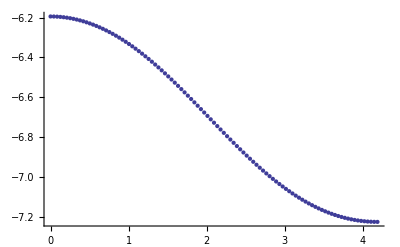

```mathematica
ListPlot[Table[{s vecL/3.,Sort[Eigenvalues[H[s vec/3.]]][[1]]},{s,0.,1.,0.01}]]
```

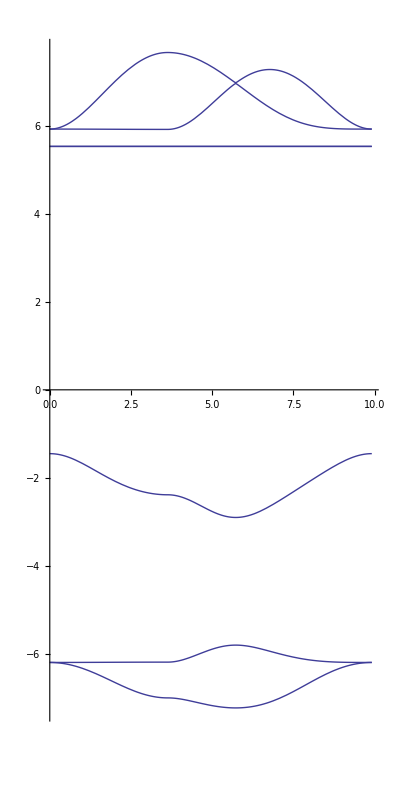

```mathematica
Plot[Sort[Eigenvalues[H[If[(vecL/3.+vecL/6.+2. π/√3.-s)<vecL/3.+vecL/6.,(vecL/3.+vecL/6.+2. π/√3.-s),vecL/3.+vecL/6.] vec/vecL+If[(vecL/3.+vecL/6.+2. π/√3.-s)<vecL/3.+vecL/6.,0.,(vecL/3.+vecL/6.+2. π/√3.-s)-(vecL/3.+vecL/6.)] vec1/vec1L]]//Re],{s,0.,vecL/3.+vecL/6.+2. π/√3.},AspectRatio->2,PlotStyle->Thick]
```

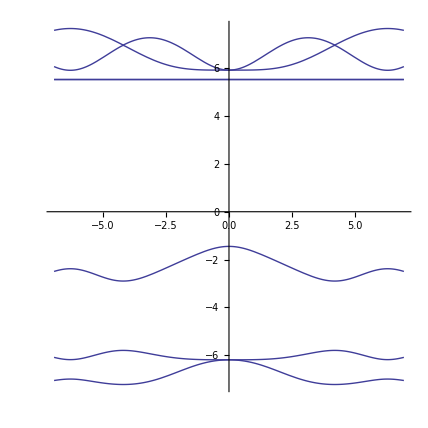

```mathematica
Plot[Sort[Eigenvalues[H[{kx,0.}]]],{kx,-4.*√3.,4.*√3.},AspectRatio->1,PlotStyle->Thick]
```

```mathematica
?AspectRatio
```

AspectRatio is an option for Graphics and related functions which specifies the ratio of height to width for a plot.

## Three orbital model

### Parameters

#### MoS2 (LDA)

```mathematica
Δ1=1.238;
Δ2=2.366;
t0=-0.218;
t1=0.444;
t2=0.533;
t11=0.250;
t12=0.360;
t22=0.047;
ll=0.;
```

```mathematica
Clear[Δ1,Δ2,t0,t1,t2,t11,t12,t22,ll];
```

#### WSe2 (GGA)

```mathematica
Δ1=0.943;
Δ2=2.179;
t0=-0.207;
t1=0.457;
t2=0.486;
t11=0.263;
t12=0.329;
t22=0.034;
ll=0.228;
```

#### General (units of t0) with varying t22

List from “Three band model GGA” PRB 88, 085433 (2013)

```mathematica
MoS2={1.046,2.104,−0.184,0.401,0.507,0.218,0.338,0.057,0.073};
WS2={1.130,2.275,−0.206,0.567,0.536,0.286,0.384,−0.061,0.211};
MoSe2={0.919,2.065,−0.188,0.317,0.456,0.211,0.290,0.130,0.091};
WSe2={0.943,2.179,−0.207,0.457,0.486,0.263,0.329,0.034,0.228};
MoTe2={0.605,1.972,−0.169,0.228,0.390,0.207,0.239,0.252,0.107};
WTe2={0.606,2.102,−0.175,0.342,0.410,0.233,0.270,0.190,0.237};
```

```mathematica
{MoS2/(0.184),WS2/(0.206),MoSe2/(0.188),WSe2/(0.207),MoTe2/(0.169),WTe2/(0.175)}
```

{{5.68478,11.4348,-1.,2.17935,2.75543,1.18478,1.83696,0.309783,0.396739},{5.48544,11.0437,-1.,2.75243,2.60194,1.38835,1.86408,-0.296117,1.02427},{4.8883,10.984,-1.,1.68617,2.42553,1.12234,1.54255,0.691489,0.484043},{4.55556,10.5266,-1.,2.20773,2.34783,1.27053,1.58937,0.164251,1.10145},{3.57988,11.6686,-1.,1.34911,2.30769,1.22485,1.4142,1.49112,0.633136},{3.46286,12.0114,-1.,1.95429,2.34286,1.33143,1.54286,1.08571,1.35429}}

```mathematica
paramsList={{5.684782608695652,11.434782608695652,-1.,2.1793478260869565,2.755434782608696,1.184782608695652,1.8369565217391306,0.3097826086956522},{5.485436893203883,11.043689320388351,-1.,2.7524271844660193,2.601941747572816,1.3883495145631068,1.864077669902913,-0.29611650485436897},{4.888297872340425,10.98404255319149,-1.,1.6861702127659575,2.425531914893617,1.122340425531915,1.5425531914893615,0.6914893617021277},{4.555555555555555,10.526570048309178,-1.,2.207729468599034,2.347826086956522,1.2705314009661837,1.5893719806763287,0.1642512077294686},{3.5798816568047336,11.668639053254438,-1.,1.349112426035503,2.307692307692308,1.2248520710059172,1.4142011834319526,1.4911242603550297},{3.4628571428571426,12.01142857142857,-1.,1.9542857142857144,2.342857142857143,1.3314285714285716,1.542857142857143,1.0857142857142859}};
```

Average value

```mathematica
avg=Table[Sum[paramsList[[i,j]],{i,1,6}]/6,{j,1,8}]
```

{4.60947,11.2782,-1.,2.02151,2.46355,1.25371,1.63167,0.574374}

Relative deviation (percentage)

```mathematica
Table[Table[Abs[paramsList[[i,j]]-avg[[j]]]*100/Abs[paramsList[[i,j]]],{j,1,8}],{i,1,6}]
```

{{18.9157,1.36942,0.,7.24234,10.5932,5.81807,11.1754,85.412},{15.969,2.12341,0.,26.5553,5.31889,9.69752,12.4677,293.969},{5.70402,2.67797,0.,19.8878,1.5673,11.7053,5.7772,16.9367},{1.18346,7.14024,0.,8.43479,4.92887,1.32364,2.66128,249.693},{28.7604,3.34612,0.,49.8402,6.75372,2.35637,15.3775,61.4805},{33.1117,6.10449,0.,3.43995,5.15141,5.83692,5.75636,47.0971}}

```mathematica
{{18.91565713479669,1.3694233478354565,0.,7.2423357800494665,10.59315408300714,5.818070715841579,11.175381904446919,85.41202349677303},{15.96897911108816,2.123409113444242,0.,26.555290904136626,5.318889912571316,9.697515967866122,12.467723777780096,293.9689932198066},{5.704015140769136,2.6779709862011507,0.,19.887786144109704,1.567302219490027,11.705332016743531,5.777202628632423,16.93665368764967},{1.1834575467953397,7.140236317427024,0.,8.43478934086393,4.928867777581893,1.3236431822808217,2.661279728978901,249.69252960972267},{28.76036314816252,3.3461231047985383,0.,49.84015414096653,6.753717651974621,2.356368444471621,15.377474869342002,61.48046018063288},{33.11171761977568,6.104490745545164,0.,3.4399486180242245,5.151410445190767,5.83692391749031,5.756363936231179,47.09711286097509}}
```

Values to be used

```mathematica
usedAvg={4.6,11.3,-1.,2.0,2.5,1.3,1.6,0.5};
```

```mathematica
usedWSe2={4.6,10.5,-1.,2.2,2.3,1.3,1.6,0.16};
```

Relative error (percentage)

```mathematica
Table[Table[Abs[paramsList[[i,j]]-usedAvg[[j]]]*100/Abs[paramsList[[i,j]]],{j,1,8}],{i,1,6}]
```

{{19.0822,1.17871,0.,8.22943,9.27022,9.72477,12.8994,61.4035},{16.1416,2.32088,0.,27.3369,3.91791,6.36364,14.1667,268.852},{5.89771,2.87651,0.,18.612,3.07018,15.8294,3.72414,27.6923},{0.97561,7.34741,0.,9.40919,6.48148,2.31939,0.668693,204.412},{28.4959,3.15923,0.,48.2456,8.33333,6.13527,13.1381,66.4683},{32.8383,5.92293,0.,2.33918,6.70732,2.36052,3.7037,53.9474}}

```mathematica
Δ1=4.6;
Δ2=11.3;
t0=-1.;
t1=2.0;
t2=2.5;
t11=1.3;
t12=1.6;
t22=1.2;
ll=0.;
```

```mathematica
Table[Table[Abs[paramsList[[i,j]]-usedWSe2[[j]]]*100/Abs[paramsList[[i,j]]],{j,1,8}],{i,1,6}]
```

{{19.0822,8.1749,0.,0.947631,16.5286,9.72477,12.8994,48.3509},{16.1416,4.92308,0.,20.0705,11.6045,6.36364,14.1667,154.033},{5.89771,4.40678,0.,30.4732,5.17544,15.8294,3.72414,76.8615},{0.97561,0.252409,0.,0.350109,2.03704,2.31939,0.668693,2.58824},{28.4959,10.0152,0.,63.0702,0.333333,6.13527,13.1381,89.2698},{32.8383,12.5833,0.,12.5731,1.82927,2.36052,3.7037,85.2632}}

```mathematica
Δ1=4.6;
Δ2=10.5;
t0=-1.;
t1=2.2;
t2=2.3;
t11=1.3;
t12=1.6;
t22=0.16;
ll=0.;
Clear[Δ1,Δ2,t0,t1,t2,t11,t12,t22,ll];
```

```mathematica
Δ1=5.684782608695652;
Δ2=11.434782608695652;
t0=-1.;
t1=2.1793478260869565;
t2=2.755434782608696;
t11=1.184782608695652;
t12=1.83695652173913;
t22=0.3097826086956522;
ll=0.3967391304347826;
{5.684782608695652,11.434782608695652,-1.,2.1793478260869565,2.755434782608696,1.184782608695652,1.8369565217391306,0.3097826086956522,0.3967391304347826}
```

{5.68478,11.4348,-1.,2.17935,2.75543,1.18478,1.83696,0.309783,0.396739}

### Hamiltonian matrices

#### r, r

```mathematica
Hrr=Table[0.,{i,1,3},{j,1,3}];

Hrr[[1,1]]=Δ1;
Hrr[[2,2]]=Δ2;
Hrr[[3,3]]=Δ2;
```

#### r, r with SO

```mathematica
Hrru=Table[0.,{i,1,3},{j,1,3}];
Hrrd=Table[0.,{i,1,3},{j,1,3}];

Hrru[[1,1]]=Δ1;
Hrru[[2,2]]=Δ2;
Hrru[[3,3]]=Δ2;
Hrru[[2,3]]=+ ll ⅈ;
Hrru[[3,2]]=- ll ⅈ;

Hrrd[[1,1]]=Δ1;
Hrrd[[2,2]]=Δ2;
Hrrd[[3,3]]=Δ2;
Hrrd[[2,3]]=- ll ⅈ;
Hrrd[[3,2]]=+ ll ⅈ;
```

#### r, r+a1

```mathematica
Hrra1=Table[0.,{i,1,3},{j,1,3}];

Hrra1[[1,1]]=t0;
Hrra1[[1,2]]=t1;
Hrra1[[1,3]]=t2;

Hrra1[[2,1]]=-t1;
Hrra1[[2,2]]=t11;
Hrra1[[2,3]]=t12;

Hrra1[[3,1]]=t2;
Hrra1[[3,2]]=-t12;
Hrra1[[3,3]]=t22;
```

#### r, r+a2

```mathematica
Hrra2=Table[0.,{i,1,3},{j,1,3}];

Hrra2[[1,1]]=t0;
Hrra2[[1,2]]=t1/2.-t2√3./2.;
Hrra2[[1,3]]=-t1√3./2.-t2/2.;

Hrra2[[2,1]]=-t1/2.-t2√3./2.;
Hrra2[[2,2]]=t11/4.+t22 3./4.;
Hrra2[[2,3]]=(√3.)/4.(t22-t11)-t12;

Hrra2[[3,1]]=t1√3./2.-t2/2.;
Hrra2[[3,2]]=(√3.)/4.(t22-t11)+t12;
Hrra2[[3,3]]=t11 3./4.+t22/4.;
```

#### r, r+a2-a1

```mathematica
Hrra2ma1=Table[0.,{i,1,3},{j,1,3}];

Hrra2ma1[[1,1]]=t0;
Hrra2ma1[[1,2]]=-t1/2.+t2√3./2.;
Hrra2ma1[[1,3]]=-t1√3./2.-t2/2.;

Hrra2ma1[[2,1]]=t1/2.+t2√3./2.;
Hrra2ma1[[2,2]]=t11/4.+t22 3./4.;
Hrra2ma1[[2,3]]=-(√3.)/4.(t22-t11)+t12;

Hrra2ma1[[3,1]]=t1√3./2.-t2/2.;
Hrra2ma1[[3,2]]=-(√3.)/4.(t22-t11)-t12;
Hrra2ma1[[3,3]]=t11 3./4.+t22/4.;
```

#### r, r-a1

```mathematica
Hrra1m=Table[0.,{i,1,3},{j,1,3}];

Hrra1m[[1,1]]=t0;
Hrra1m[[1,2]]=-t1;
Hrra1m[[1,3]]=t2;

Hrra1m[[2,1]]=t1;
Hrra1m[[2,2]]=t11;
Hrra1m[[2,3]]=-t12;

Hrra1m[[3,1]]=t2;
Hrra1m[[3,2]]=t12;
Hrra1m[[3,3]]=t22;
```

#### r, r-a2

```mathematica
Hrra2m=Table[0.,{i,1,3},{j,1,3}];

Hrra2m[[1,1]]=t0;
Hrra2m[[1,2]]=-t1/2.-t2√3./2.;
Hrra2m[[1,3]]=t1√3./2.-t2/2.;

Hrra2m[[2,1]]=t1/2.-t2√3./2.;
Hrra2m[[2,2]]=t11/4.+t22 3./4.;
Hrra2m[[2,3]]=(√3.)/4.(t22-t11)+t12;

Hrra2m[[3,1]]=-t1√3./2.-t2/2.;
Hrra2m[[3,2]]=(√3.)/4.(t22-t11)-t12;
Hrra2m[[3,3]]=t11 3./4.+t22/4.;
```

#### r, r+a1-a2

```mathematica
Hrra1ma2=Table[0.,{i,1,3},{j,1,3}];

Hrra1ma2[[1,1]]=t0;
Hrra1ma2[[1,2]]=t1/2.+t2√3./2.;
Hrra1ma2[[1,3]]=t1√3./2.-t2/2.;

Hrra1ma2[[2,1]]=-t1/2.+t2√3./2.;
Hrra1ma2[[2,2]]=t11/4.+t22 3./4.;
Hrra1ma2[[2,3]]=-(√3.)/4.(t22-t11)-t12;

Hrra1ma2[[3,1]]=-t1√3./2.-t2/2.;
Hrra1ma2[[3,2]]=-(√3.)/4.(t22-t11)+t12;
Hrra1ma2[[3,3]]=t11 3./4.+t22/4.;
```

### Hamiltonian k-sapce

#### Defenitions

```mathematica
a1={1,0};
a2={1./2.,-(√3.)/2.};
b1=2. π 2./(√3.){(√3.)/2.,1./2.};
b2=2. π 2./(√3.){0.,-1.};
```

#### Hamiltonian

```mathematica
HnoSO[k_]:=Hrr+Hrra1 ⅇ^(-ⅈ k.a1)+Hrra1m ⅇ^(ⅈ k.a1)+Hrra2m ⅇ^(ⅈ k.a2)+Hrra2 ⅇ^(-ⅈ k.a2)+Hrra2ma1 ⅇ^(-ⅈ k.(a2-a1))+Hrra1ma2 ⅇ^(-ⅈ k.(a1-a2));
```

```mathematica
Hu[k_]:=Hrru+Hrra1 ⅇ^(-ⅈ k.a1)+Hrra1m ⅇ^(ⅈ k.a1)+Hrra2m ⅇ^(ⅈ k.a2)+Hrra2 ⅇ^(-ⅈ k.a2)+Hrra2ma1 ⅇ^(-ⅈ k.(a2-a1))+Hrra1ma2 ⅇ^(-ⅈ k.(a1-a2));
Hd[k_]:=Hrrd+Hrra1 ⅇ^(-ⅈ k.a1)+Hrra1m ⅇ^(ⅈ k.a1)+Hrra2m ⅇ^(ⅈ k.a2)+Hrra2 ⅇ^(-ⅈ k.a2)+Hrra2ma1 ⅇ^(-ⅈ k.(a2-a1))+Hrra1ma2 ⅇ^(-ⅈ k.(a1-a2));
```

### Spectrum

```mathematica
vec=b2+2. b1;
vecL=Sqrt[vec.vec];
vec1=b2/2.;
vec1L=Sqrt[vec1.vec1];
```

```mathematica
Table[{s vecL/3.,Sort[Eigenvalues[HnoSO[s vec/3.]]//Re][[1]]},{s,0.,1.,0.1}]
```

{{0.,-0.315217},{0.418879,-0.506682},{0.837758,-1.00629},{1.25664,-1.65698},{1.67552,-2.3047},{2.0944,-2.7954},{2.51327,-2.95562},{2.93215,-2.6405},{3.35103,-1.84353},{3.76991,-0.849719},{4.18879,-0.352171}}

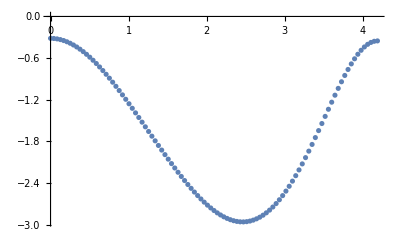

```mathematica
ListPlot[Table[{s vecL/3.,Sort[Eigenvalues[HnoSO[s vec/3.]]//Re][[1]]},{s,0.,1.,0.01}]]
```

#### Γ-M-K-Γ

Without SOC

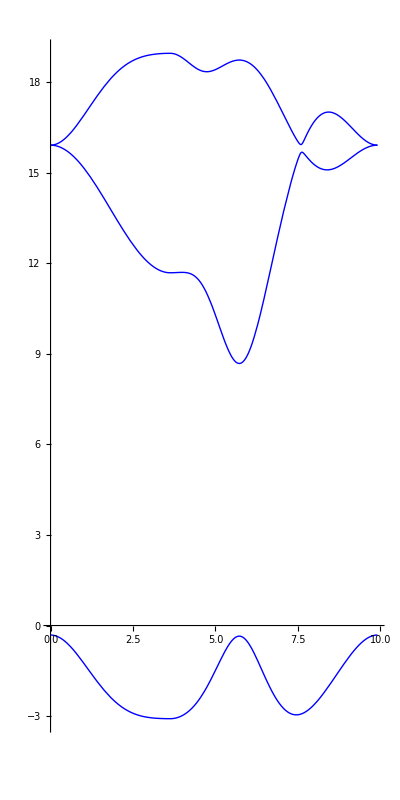

```mathematica
fig=Plot[{Sort[Eigenvalues[HnoSO[If[(vecL/3.+vecL/6.+2. π/√3.-s)<vecL/3.+vecL/6.,(vecL/3.+vecL/6.+2. π/√3.-s),vecL/3.+vecL/6.] vec/vecL+If[(vecL/3.+vecL/6.+2. π/√3.-s)<vecL/3.+vecL/6.,0.,(vecL/3.+vecL/6.+2. π/√3.-s)-(vecL/3.+vecL/6.)] vec1/vec1L]]//Re]},{s,0.,vecL/3.+vecL/6.+2. π/√3.},AspectRatio->2,PlotStyle->{Thick,Blue}]
```

```mathematica
data=Table[Flatten[{s,Sort[Eigenvalues[HnoSO[If[(vecL/3.+vecL/6.+2. π/√3.-s)<vecL/3.+vecL/6.,(vecL/3.+vecL/6.+2. π/√3.-s),vecL/3.+vecL/6.] vec/vecL+If[(vecL/3.+vecL/6.+2. π/√3.-s)<vecL/3.+vecL/6.,0.,(vecL/3.+vecL/6.+2. π/√3.-s)-(vecL/3.+vecL/6.)] vec1/vec1L]]//Re]}],{s,0.,vecL/3.+vecL/6.+2. π/√3.,(vecL/3.+vecL/6.+2. π/√3.)/400.}];
```

```mathematica
data1=Table[{data[[i,1]],data[[i,2]]},{i,1,Length[data]}];
data2=Table[{data[[i,1]],data[[i,3]]},{i,1,Length[data]}];
data3=Table[{data[[i,1]],data[[i,4]]},{i,1,Length[data]}];
```

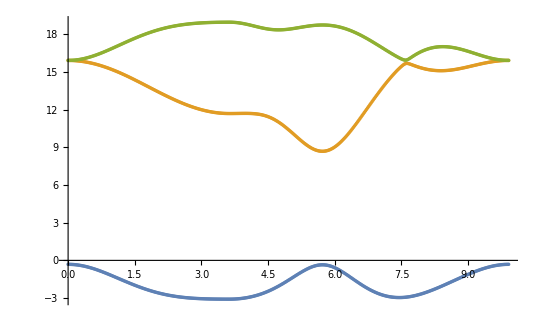

```mathematica
ListPlot[{data1,data2,data3}]
```

```mathematica
dataExport=Flatten[{Table[{data[[i,1]],data[[i,2]],data[[i,3]],data[[i,4]]},{i,1,Length[data]}],{""}},1];
Export["bands-3orbModel_WSe2_noSOC_Units-t0.dat",dataExport];
```

```mathematica
ll=vecL/3.+vecL/6.+2. π/√3.
Print["Γ="];0
Print["M="];(√3./2.)*ll/(√3./2.+3./2.)
Print["K="];(√3./2.+1./2.)*ll/(√3./2.+3./2.)
Print["Γ="];ll
```

9.91078

Γ=

0

M=

3.6276

K=

5.72199

Γ=

9.91078

Filling density versus Fermi energy

```mathematica
occupation[ener_,Ek_]:=Module[{i=1,count=0.},While[i≤3&&Ek[[i]]<ener,++i];i-1];
filling[ener_,listE_,Ni_,Nj_]:=Table[occupation[ener,listE[[i,j]]],{i,1,Ni},{j,1,Nj}]//Flatten//Total;
```

```mathematica
Nx=20;
Ny = 20;
NE=1000;
Emin=-4.;
Emax=20.;
listEigv=Table[Sort[Eigenvalues[HnoSO[i b1/Nx+j b2/Ny]]//Re],{i,1,Nx},{j,1,N}];
fillingVsE=Table[{EE=Emin+i (Emax-Emin)/NE;EE,filling[EE,listEigv,NN,NN]/(1.NN*NN)},{i,1,NE}];
```

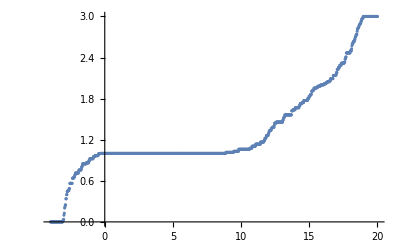

```mathematica
ListPlot[fillingVsE]
```

```mathematica
SetDirectory[NotebookDirectory[]]
dataExport=Flatten[{Table[{fillingVsE[[i,2]],fillingVsE[[i,1]]},{i,1,Length[fillingVsE]}],{""}},1];
Export["filling-E_3orbModel_WSe2_noSOC_Units-t0.csv",dataExport];
```

/Users/franciscobrito/Downloads

With SOC

```mathematica
fig=Plot[{Sort[Eigenvalues[Hu[If[(vecL/3.+vecL/6.+2. π/√3.-s)<vecL/3.+vecL/6.,(vecL/3.+vecL/6.+2. π/√3.-s),vecL/3.+vecL/6.] vec/vecL+If[(vecL/3.+vecL/6.+2. π/√3.-s)<vecL/3.+vecL/6.,0.,(vecL/3.+vecL/6.+2. π/√3.-s)-(vecL/3.+vecL/6.)] vec1/vec1L]]//Re],

Sort[Eigenvalues[Hd[If[(vecL/3.+vecL/6.+2. π/√3.-s)<vecL/3.+vecL/6.,(vecL/3.+vecL/6.+2. π/√3.-s),vecL/3.+vecL/6.] vec/vecL+If[(vecL/3.+vecL/6.+2. π/√3.-s)<vecL/3.+vecL/6.,0.,(vecL/3.+vecL/6.+2. π/√3.-s)-(vecL/3.+vecL/6.)] vec1/vec1L]]//Re]},{s,0.,vecL/3.+vecL/6.+2. π/√3.},AspectRatio->2,PlotStyle->{Thick,Blue}]
```

-Graphics-

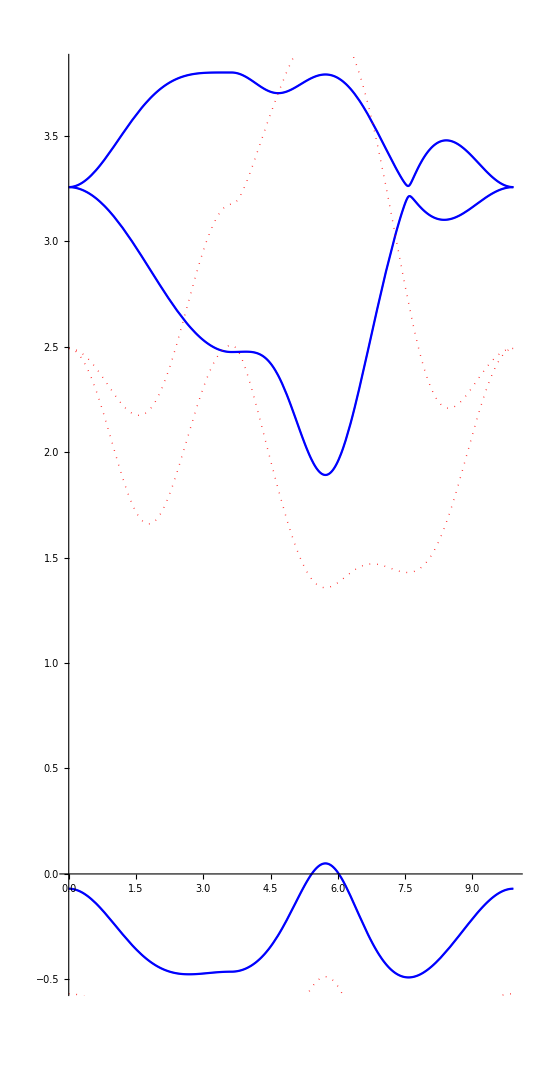

```mathematica
Show[{fig,fig1}]
```

#### Gap

```mathematica
Eigenvalues[Hu[vec/3.]]
```

```mathematica
{12.725114872174395+2.5886032416430094*^-16 ⅈ,8.983885127825623-4.254707463493033*^-17 ⅈ,5.254+5.731355395660717*^-18 ⅈ}
```

```mathematica
{3.791114872174389-3.7452530255781793*^-16 ⅈ,1.892+3.697785493223493*^-32 ⅈ,0.04988512782561279-6.956390729224466*^-17 ⅈ}
```

```mathematica
1.892-0.04988512782561279
```

1.84211

11 orbital model

```mathematica
{-9.379075432081187,-6.600164475798505,4.040539475798506,-2.642045706274525,1.3572957062745248,-0.4875495679188135}
```

```mathematica
1.3572957062745248-(-0.4875495679188135)
```

1.84485

#### Shift

```mathematica
1.892-1.3572957062745248
```

0.534704

#### Γ-K-M-K’-Γ

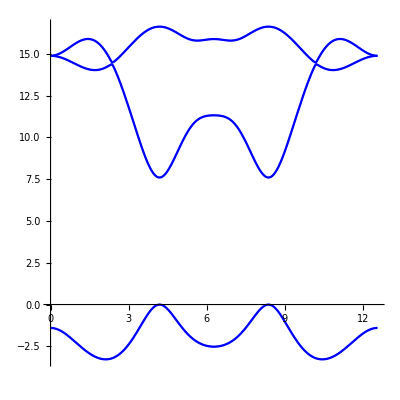

```mathematica
fig=Plot[{Sort[Eigenvalues[Hu[(vecL-s) vec/vecL]]//Re],
Sort[Eigenvalues[Hd[(vecL-s) vec/vecL]]//Re]},{s,0.,vecL},AspectRatio->1,PlotStyle->{Thick,Blue},PlotRange->All]
```

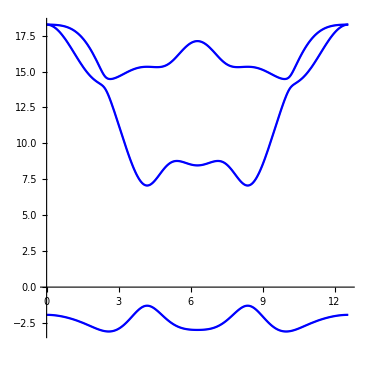
```mathematica
t22=1.2
-Graphics-
```

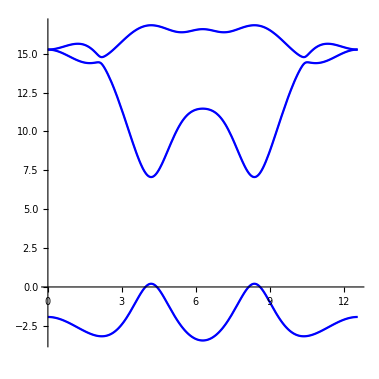
```mathematica
t22=0.2
-Graphics-
```

#### Study variation with t22

Hamiltonian

```mathematica
Hrr=Table[0.,{i,1,3},{j,1,3}];

Hrr[[1,1]]=Δ1;
Hrr[[2,2]]=Δ2;
Hrr[[3,3]]=Δ2;

Hrra1M[t22_]:=({{t0, t1, t2}, {-t1, t11, t12}, {t2, -t12, t22}});
Hrra1mM[t22_]:=({{t0, -t1, t2}, {t1, t11, -t12}, {t2, t12, t22}});
Hrra2M[t22_]:=({{t0, t1/2.-t2√3./2., -t1√3./2.-t2/2.}, {-t1/2.-t2√3./2., t11/4.+t22 3./4., (√3.)/4.(t22-t11)-t12}, {t1√3./2.-t2/2., (√3.)/4.(t22-t11)+t12, t11 3./4.+t22/4.}});
Hrra2mM[t22_]:=({{t0, -t1/2.-t2√3./2., t1√3./2.-t2/2.}, {t1/2.-t2√3./2., t11/4.+t22 3./4., (√3.)/4.(t22-t11)+t12}, {-t1√3./2.-t2/2., (√3.)/4.(t22-t11)-t12, t11 3./4.+t22/4.}});
Hrra2ma1M[t22_]:=({{t0, -t1/2.+t2√3./2., -t1√3./2.-t2/2.}, {t1/2.+t2√3./2., t11/4.+t22 3./4., -(√3.)/4.(t22-t11)+t12}, {t1√3./2.-t2/2., -(√3.)/4.(t22-t11)-t12, t11 3./4.+t22/4.}});
Hrra1ma2M[t22_]:=({{t0, t1/2.+t2√3./2., t1√3./2.-t2/2.}, {-t1/2.+t2√3./2., t11/4.+t22 3./4., -(√3.)/4.(t22-t11)-t12}, {-t1√3./2.-t2/2., -(√3.)/4.(t22-t11)+t12, t11 3./4.+t22/4.}});
H[k_,t22_]:=Hrr+Hrra1M[t22] ⅇ^(-ⅈ k.a1)+Hrra1mM[t22] ⅇ^(ⅈ k.a1)+Hrra2mM[t22] ⅇ^(ⅈ k.a2)+Hrra2M[t22] ⅇ^(-ⅈ k.a2)+Hrra2ma1M[t22] ⅇ^(-ⅈ k.(a2-a1))+Hrra1ma2M[t22] ⅇ^(-ⅈ k.(a1-a2));
```

Plot bands

```mathematica
Animate[ListPlot[Table[Sort[ener=Eigenvalues[H[s vec/vecL,t22]]//Re];Table[{s,ener[[i]]},{i,1,3}],{s,0,vecL,vecL/40}],PlotStyle->Gray],{t22,-0.3,1.2}]
```